## First some definitions (again)

```mathematica
ZeVars8=Table[allGraphs5[k,"colofour"],{k,Select[allGraphs5AtomKeys,allGraphs5[#,"comp"]===GreaterEqual& ]}]
```

{v1x2x3x45,v1x2x35x4,v1x2x34x5,v1x25x3x4,v1x25x34,v1x24x3x5,v1x24x35,v1x245x3,v1x23x4x5,v1x235x4,v15x2x3x4,v15x24x3,v14x2x3x5,v14x2x35,v14x25x3,v14x23x5,v14x235,v13x2x4x5,v13x2x45,v13x25x4,v13x24x5,v13x245,v135x2x4,v135x24,v134x2x5,v134x25,v12x3x4x5,v12x35x4,v124x3x5,v124x35}

```mathematica
ZeVars8//Length
```

30

```mathematica
buddies=Block[{
sols={},
todo=ZeVars8,
i,
current,
buddy,
antibuddy,
range=Map[ListofVars,ExpressionToList[allCrit]],
qua=Table[allGraphs5[k,"colofour"],{k,quads}]
},
todo=Select[todo,!MemberQ[qua,#]&];
For[i=1,Length[todo]≠0,i++,
current=todo[[1]];
buddy=Join[{current},Buddy[current,range]]//DeleteDuplicates;
antibuddy=Join[AntiBuddy[current,range]];
AppendTo[sols,{buddy,antibuddy}];
todo=Select[todo,!MemberQ[buddy,#]&&!MemberQ[antibuddy,#]&];
];
Select[sols,Length[#[[1]]]≠1&]
]
```

{{{v1x2x3x45,v13x245},{v1x245x3,v13x2x45}},{{v1x2x34x5,v134x25},{v1x25x34,v134x2x5}},{{v1x23x4x5,v14x235},{v1x235x4,v14x23x5}},{{v15x2x3x4,v135x24},{v15x24x3,v135x2x4}},{{v12x3x4x5,v124x35},{v12x35x4,v124x3x5}}}

```mathematica
buddyCombinations=Table[With[
{chooser=PadLeft[IntegerDigits[comb,2],5]},
Flatten[Table[buddies[[b,chooser[[b]]+1]],{b,1,5}]]],{comb,0,31}]
```

{{v1x2x3x45,v13x245,v1x2x34x5,v134x25,v1x23x4x5,v14x235,v15x2x3x4,v135x24,v12x3x4x5,v124x35},{v1x2x3x45,v13x245,v1x2x34x5,v134x25,v1x23x4x5,v14x235,v15x2x3x4,v135x24,v12x35x4,v124x3x5},{v1x2x3x45,v13x245,v1x2x34x5,v134x25,v1x23x4x5,v14x235,v15x24x3,v135x2x4,v12x3x4x5,v124x35},{v1x2x3x45,v13x245,v1x2x34x5,v134x25,v1x23x4x5,v14x235,v15x24x3,v135x2x4,v12x35x4,v124x3x5},{v1x2x3x45,v13x245,v1x2x34x5,v134x25,v1x235x4,v14x23x5,v15x2x3x4,v135x24,v12x3x4x5,v124x35},{v1x2x3x45,v13x245,v1x2x34x5,v134x25,v1x235x4,v14x23x5,v15x2x3x4,v135x24,v12x35x4,v124x3x5},{v1x2x3x45,v13x245,v1x2x34x5,v134x25,v1x235x4,v14x23x5,v15x24x3,v135x2x4,v12x3x4x5,v124x35},{v1x2x3x45,v13x245,v1x2x34x5,v134x25,v1x235x4,v14x23x5,v15x24x3,v135x2x4,v12x35x4,v124x3x5},{v1x2x3x45,v13x245,v1x25x34,v134x2x5,v1x23x4x5,v14x235,v15x2x3x4,v135x24,v12x3x4x5,v124x35},{v1x2x3x45,v13x245,v1x25x34,v134x2x5,v1x23x4x5,v14x235,v15x2x3x4,v135x24,v12x35x4,v124x3x5},{v1x2x3x45,v13x245,v1x25x34,v134x2x5,v1x23x4x5,v14x235,v15x24x3,v135x2x4,v12x3x4x5,v124x35},{v1x2x3x45,v13x245,v1x25x34,v134x2x5,v1x23x4x5,v14x235,v15x24x3,v135x2x4,v12x35x4,v124x3x5},{v1x2x3x45,v13x245,v1x25x34,v134x2x5,v1x235x4,v14x23x5,v15x2x3x4,v135x24,v12x3x4x5,v124x35},{v1x2x3x45,v13x245,v1x25x34,v134x2x5,v1x235x4,v14x23x5,v15x2x3x4,v135x24,v12x35x4,v124x3x5},{v1x2x3x45,v13x245,v1x25x34,v134x2x5,v1x235x4,v14x23x5,v15x24x3,v135x2x4,v12x3x4x5,v124x35},{v1x2x3x45,v13x245,v1x25x34,v134x2x5,v1x235x4,v14x23x5,v15x24x3,v135x2x4,v12x35x4,v124x3x5},{v1x245x3,v13x2x45,v1x2x34x5,v134x25,v1x23x4x5,v14x235,v15x2x3x4,v135x24,v12x3x4x5,v124x35},{v1x245x3,v13x2x45,v1x2x34x5,v134x25,v1x23x4x5,v14x235,v15x2x3x4,v135x24,v12x35x4,v124x3x5},{v1x245x3,v13x2x45,v1x2x34x5,v134x25,v1x23x4x5,v14x235,v15x24x3,v135x2x4,v12x3x4x5,v124x35},{v1x245x3,v13x2x45,v1x2x34x5,v134x25,v1x23x4x5,v14x235,v15x24x3,v135x2x4,v12x35x4,v124x3x5},{v1x245x3,v13x2x45,v1x2x34x5,v134x25,v1x235x4,v14x23x5,v15x2x3x4,v135x24,v12x3x4x5,v124x35},{v1x245x3,v13x2x45,v1x2x34x5,v134x25,v1x235x4,v14x23x5,v15x2x3x4,v135x24,v12x35x4,v124x3x5},{v1x245x3,v13x2x45,v1x2x34x5,v134x25,v1x235x4,v14x23x5,v15x24x3,v135x2x4,v12x3x4x5,v124x35},{v1x245x3,v13x2x45,v1x2x34x5,v134x25,v1x235x4,v14x23x5,v15x24x3,v135x2x4,v12x35x4,v124x3x5},{v1x245x3,v13x2x45,v1x25x34,v134x2x5,v1x23x4x5,v14x235,v15x2x3x4,v135x24,v12x3x4x5,v124x35},{v1x245x3,v13x2x45,v1x25x34,v134x2x5,v1x23x4x5,v14x235,v15x2x3x4,v135x24,v12x35x4,v124x3x5},{v1x245x3,v13x2x45,v1x25x34,v134x2x5,v1x23x4x5,v14x235,v15x24x3,v135x2x4,v12x3x4x5,v124x35},{v1x245x3,v13x2x45,v1x25x34,v134x2x5,v1x23x4x5,v14x235,v15x24x3,v135x2x4,v12x35x4,v124x3x5},{v1x245x3,v13x2x45,v1x25x34,v134x2x5,v1x235x4,v14x23x5,v15x2x3x4,v135x24,v12x3x4x5,v124x35},{v1x245x3,v13x2x45,v1x25x34,v134x2x5,v1x235x4,v14x23x5,v15x2x3x4,v135x24,v12x35x4,v124x3x5},{v1x245x3,v13x2x45,v1x25x34,v134x2x5,v1x235x4,v14x23x5,v15x24x3,v135x2x4,v12x3x4x5,v124x35},{v1x245x3,v13x2x45,v1x25x34,v134x2x5,v1x235x4,v14x23x5,v15x24x3,v135x2x4,v12x35x4,v124x3x5}}

```mathematica
PropagateComp[]:=Block[{leftKey,rightKey,left,right,current,changed=0},
Monitor[
Table[
current = allGraphs5[k];
Table[
leftKey=children[[1]];
rightKey=children[[2]];
left=allGraphs5[leftKey];
right=allGraphs5[rightKey];
If[current["comp"]===GreaterEqual && (left["comp"]===Greater),
current["compwhy"]="The relation holds "<> ToString[k]<> "("<>ToString[current["comp"]]<> ")== "<> ToString[leftKey]<>"("<>ToString[left["comp"]]<> ") + "<> ToString[rightKey]<> 
" (" <>ToString[right["comp"]]<>") (greater propagated from left)";
current["comp"]=Greater;
PrintTemporary[current["compwhy"]];
changed++;
allGraphs5[k]=current;
];

If[current["comp"]===GreaterEqual && (right["comp"]===Greater),
current["compwhy"]="The relation holds "<> ToString[k]<> "("<>ToString[current["comp"]]<> ")== "<> ToString[leftKey]<>"("<>ToString[left["comp"]]<> ") + "<> ToString[rightKey]<> 
" (" <>ToString[right["comp"]]<>") (greater propagated from right)";
current["comp"]=Greater;
PrintTemporary[current["compwhy"]];
changed++;
allGraphs5[k]=current;
];

If[current["comp"]===GreaterEqual && (left["comp"]===Equal&&right["comp"]===Equal),
current["compwhy"]="The relation holds "<> ToString[k]<> "("<>ToString[current["comp"]]<> ")== "<> ToString[leftKey]<>"("<>ToString[left["comp"]]<> ") + "<> ToString[rightKey]<> 
" (" <>ToString[right["comp"]]<>") (zero propagated)";
current["comp"]=Equal;
PrintTemporary[current["compwhy"]];
changed++;
allGraphs5[k]=current;
];
If[current["comp"]===GreaterEqual && (left["comp"]===Equal&&right["comp"]===Greater),
current["compwhy"]="The relation holds "<> ToString[k]<> "("<>ToString[current["comp"]]<> ")== "<> ToString[leftKey]<>"("<>ToString[left["comp"]]<> ") + "<> ToString[rightKey]<> 
" (" <>ToString[right["comp"]]<>") (Greater (right) and zero (left) propagated)";
current["comp"]=Greater;
PrintTemporary[current["compwhy"]];
changed++;
allGraphs5[k]=current;
];

If[current["comp"]===GreaterEqual && (left["comp"]===Greater&&right["comp"]===Equal),
current["compwhy"]="The relation holds "<> ToString[k]<> "("<>ToString[current["comp"]]<> ")== "<> ToString[leftKey]<>"("<>ToString[left["comp"]]<> ") + "<> ToString[rightKey]<> 
" (" <>ToString[right["comp"]]<>") (Zero (right) and Greater (left) propagated)";
current["comp"]=Greater;
PrintTemporary[current["compwhy"]];
changed++;
allGraphs5[k]=current;
];

If[current["comp"]===Greater && (left["comp"]===GreaterEqual&&right["comp"]===Equal),
left["compwhy"]="The down relation holds "<> ToString[k]<> "("<>ToString[current["comp"]]<> ")== "<> ToString[leftKey]<>"("<>ToString[left["comp"]]<> ") + "<> ToString[rightKey]<> 
" (" <>ToString[right["comp"]]<>") (Greater(parent) and zero(right) pushed down to left)";
left["comp"]=Greater;
PrintTemporary[left["compwhy"]];
changed++;
allGraphs5[children[[1]]]=left;
];

If[current["comp"]===Greater && (left["comp"]===Equal&&right["comp"]===GreaterEqual),
right["compwhy"]="The down relation holds "<> ToString[k]<> "("<> ToString[current["comp"]]<> ") == "<> ToString[leftKey]<>"("<>ToString[left["comp"]]<> ") + "<> ToString[rightKey]<> " (" <>ToString[right["comp"]]<>") (Greater(parent) and zero(left) pushed down to right)";
right["comp"]=Greater;
PrintTemporary[right["compwhy"]];
changed++;
allGraphs5[children[[2]]]=right;
]
,{children,allGraphs5[k,"children"]}
]
,
{k,Keys[allGraphs5]}],
k
];
changed
]
```

## Now we start experiments (quads)

```mathematica
Monitor[
Table[
Block[
{backup=allGraphs5,
reason="declaring buddies "<>ToString[com]<> " positive.",
notok},
Table[
allGraphs5[k,"comp"]=Greater;
allGraphs5[k,"compwhy"]=reason;
allGraphs5[k,"atleast"]=1;
allGraphs5[k,"atleastwhy"]=reason,
{k,Join[quads,(com/.RepKey["C"])]}
];
PropagateAtLeast[];
PropagateAtLeast[];
PropagateAtLeast[];
PropagateComp[];
PropagateComp[];
PropagateComp[];

Clear[RepAtLeast];RepAtLeast[base_]:=RepAtLeast[base]=Table[allGraphs5[key,Bases[base,"Colofour"]]->allGraphs5[key,"atleast"],{key,Bases[base,"AtomKeys"]}];
notok=With[
{base="C",colofour="colofour"},
Select[Keys[allGraphs5],(allGraphs5[#,"atleast"]≠ (allGraphs5[#,colofour]/.RepAtLeast[base]))&]
];
Print[com->notok];
allGraphs5=backup;
com->notok
],{com,Take[buddyCombinations,1]}
],
{com}
];
```

{v1x2x3x45,v13x245,v1x2x34x5,v134x25,v1x23x4x5,v14x235,v15x2x3x4,v135x24,v12x3x4x5,v124x35}→{}

{v1x2x3x45,v13x245,v1x2x34x5,v134x25,v1x23x4x5,v14x235,v15x2x3x4,v135x24,v12x35x4,v124x3x5}→{}

{v1x2x3x45,v13x245,v1x2x34x5,v134x25,v1x23x4x5,v14x235,v15x24x3,v135x2x4,v12x3x4x5,v124x35}→{}

{v1x2x3x45,v13x245,v1x2x34x5,v134x25,v1x23x4x5,v14x235,v15x24x3,v135x2x4,v12x35x4,v124x3x5}→{}

{v1x2x3x45,v13x245,v1x2x34x5,v134x25,v1x235x4,v14x23x5,v15x2x3x4,v135x24,v12x3x4x5,v124x35}→{}

{v1x2x3x45,v13x245,v1x2x34x5,v134x25,v1x235x4,v14x23x5,v15x2x3x4,v135x24,v12x35x4,v124x3x5}→{}

{v1x2x3x45,v13x245,v1x2x34x5,v134x25,v1x235x4,v14x23x5,v15x24x3,v135x2x4,v12x3x4x5,v124x35}→{}

{v1x2x3x45,v13x245,v1x2x34x5,v134x25,v1x235x4,v14x23x5,v15x24x3,v135x2x4,v12x35x4,v124x3x5}→{}

{v1x2x3x45,v13x245,v1x25x34,v134x2x5,v1x23x4x5,v14x235,v15x2x3x4,v135x24,v12x3x4x5,v124x35}→{}

{v1x2x3x45,v13x245,v1x25x34,v134x2x5,v1x23x4x5,v14x235,v15x2x3x4,v135x24,v12x35x4,v124x3x5}→{}

{v1x2x3x45,v13x245,v1x25x34,v134x2x5,v1x23x4x5,v14x235,v15x24x3,v135x2x4,v12x3x4x5,v124x35}→{}

{v1x2x3x45,v13x245,v1x25x34,v134x2x5,v1x23x4x5,v14x235,v15x24x3,v135x2x4,v12x35x4,v124x3x5}→{}

{v1x2x3x45,v13x245,v1x25x34,v134x2x5,v1x235x4,v14x23x5,v15x2x3x4,v135x24,v12x3x4x5,v124x35}→{}

{v1x2x3x45,v13x245,v1x25x34,v134x2x5,v1x235x4,v14x23x5,v15x2x3x4,v135x24,v12x35x4,v124x3x5}→{}

{v1x2x3x45,v13x245,v1x25x34,v134x2x5,v1x235x4,v14x23x5,v15x24x3,v135x2x4,v12x3x4x5,v124x35}→{}

{v1x2x3x45,v13x245,v1x25x34,v134x2x5,v1x235x4,v14x23x5,v15x24x3,v135x2x4,v12x35x4,v124x3x5}→{}

{v1x245x3,v13x2x45,v1x2x34x5,v134x25,v1x23x4x5,v14x235,v15x2x3x4,v135x24,v12x3x4x5,v124x35}→{}

{v1x245x3,v13x2x45,v1x2x34x5,v134x25,v1x23x4x5,v14x235,v15x2x3x4,v135x24,v12x35x4,v124x3x5}→{}

{v1x245x3,v13x2x45,v1x2x34x5,v134x25,v1x23x4x5,v14x235,v15x24x3,v135x2x4,v12x3x4x5,v124x35}→{}

{v1x245x3,v13x2x45,v1x2x34x5,v134x25,v1x23x4x5,v14x235,v15x24x3,v135x2x4,v12x35x4,v124x3x5}→{}

{v1x245x3,v13x2x45,v1x2x34x5,v134x25,v1x235x4,v14x23x5,v15x2x3x4,v135x24,v12x3x4x5,v124x35}→{}

{v1x245x3,v13x2x45,v1x2x34x5,v134x25,v1x235x4,v14x23x5,v15x2x3x4,v135x24,v12x35x4,v124x3x5}→{}

{v1x245x3,v13x2x45,v1x2x34x5,v134x25,v1x235x4,v14x23x5,v15x24x3,v135x2x4,v12x3x4x5,v124x35}→{}

{v1x245x3,v13x2x45,v1x2x34x5,v134x25,v1x235x4,v14x23x5,v15x24x3,v135x2x4,v12x35x4,v124x3x5}→{}

{v1x245x3,v13x2x45,v1x25x34,v134x2x5,v1x23x4x5,v14x235,v15x2x3x4,v135x24,v12x3x4x5,v124x35}→{}

{v1x245x3,v13x2x45,v1x25x34,v134x2x5,v1x23x4x5,v14x235,v15x2x3x4,v135x24,v12x35x4,v124x3x5}→{}

{v1x245x3,v13x2x45,v1x25x34,v134x2x5,v1x23x4x5,v14x235,v15x24x3,v135x2x4,v12x3x4x5,v124x35}→{}

{v1x245x3,v13x2x45,v1x25x34,v134x2x5,v1x23x4x5,v14x235,v15x24x3,v135x2x4,v12x35x4,v124x3x5}→{}

{v1x245x3,v13x2x45,v1x25x34,v134x2x5,v1x235x4,v14x23x5,v15x2x3x4,v135x24,v12x3x4x5,v124x35}→{}

{v1x245x3,v13x2x45,v1x25x34,v134x2x5,v1x235x4,v14x23x5,v15x2x3x4,v135x24,v12x35x4,v124x3x5}→{}

{v1x245x3,v13x2x45,v1x25x34,v134x2x5,v1x235x4,v14x23x5,v15x24x3,v135x2x4,v12x3x4x5,v124x35}→{}

{v1x245x3,v13x2x45,v1x25x34,v134x2x5,v1x235x4,v14x23x5,v15x24x3,v135x2x4,v12x35x4,v124x3x5}→{}

## Now without the quads

```mathematica
Monitor[
Block[{pos=1},
Table[
Block[
{backup=allGraphs5,
reason="declaring buddies "<>ToString[com]<> " positive.",
notok, crit},
Table[
allGraphs5[k,"comp"]=Greater;
allGraphs5[k,"compwhy"]=reason;
allGraphs5[k,"atleast"]=1;
allGraphs5[k,"atleastwhy"]=reason,
{k,(com/.RepKey["C"])}
];
PropagateAtLeast[];
PropagateAtLeast[];
PropagateAtLeast[];
PropagateComp[];
PropagateComp[];
PropagateComp[];

Clear[RepAtLeast];RepAtLeast[base_]:=RepAtLeast[base]=Table[allGraphs5[key,Bases[base,"Colofour"]]->allGraphs5[key,"atleast"],{key,Bases[base,"AtomKeys"]}];
notok=With[
{base="C",colofour="colofour"},
Select[Keys[allGraphs5],(allGraphs5[#,"atleast"]≠ (allGraphs5[#,colofour]/.RepAtLeast[base]))&]
];
Print[com->Length[notok]];
crit=Reduce[Fold[And,Table[Fold[Or,Table[v>0,{v,ListofVars[allGraphs5[k,"colofour"]]}]],{k,notok}]]];
Put[crit,"d:\\Saved\\exppol_"<> ToString[pos++] <> ".m"];
Print[crit];
allGraphs5=backup;
],{com,buddyCombinations}
]
],
{com}
]
```

{v1x2x3x45,v13x245,v1x2x34x5,v134x25,v1x23x4x5,v14x235,v15x2x3x4,v135x24,v12x3x4x5,v124x35}→592

(v14x25x3>0&&v14x2x35>0&&v13x25x4>0&&v1x24x35>0&&v13x24x5>0)||(v14x2x35>0&&v13x25x4>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v14x2x3x5>0&&v13x25x4>0&&v1x2x35x4>0&&v13x24x5>0)||(v14x2x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v1x24x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v14x25x3>0&&v1x2x35x4>0&&v13x24x5>0)||(v14x2x35>0&&v1x25x3x4>0&&v13x24x5>0)||(v1x24x35>0&&v14x2x3x5>0&&v1x25x3x4>0&&v13x24x5>0)||(v1x25x3x4>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x24x5>0)||(v1x24x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x25x4>0)||(v1x24x3x5>0&&v14x25x3>0&&v1x2x35x4>0&&v13x25x4>0)||(v1x24x35>0&&v14x2x35>0&&v1x2x3x4x5>0&&v13x25x4>0)||(v14x2x35>0&&v1x24x3x5>0&&v13x25x4>0)||(v14x2x3x5>0&&v1x24x35>0&&v13x25x4>0)||(v1x24x3x5>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x25x4>0)||(v14x2x35>0&&v14x25x3>0&&v1x24x3x5>0&&v13x2x4x5>0)||(v14x25x3>0&&v1x24x35>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v14x25x3>0&&v1x2x35x4>0&&v13x2x4x5>0)||(v1x24x35>0&&v14x2x35>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v14x2x35>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x35>0&&v14x2x3x5>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v1x25x3x4>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x2x4x5>0)

{v1x2x3x45,v13x245,v1x2x34x5,v134x25,v1x23x4x5,v14x235,v15x2x3x4,v135x24,v12x35x4,v124x3x5}→592

(v14x25x3>0&&v14x2x35>0&&v13x25x4>0&&v1x24x35>0&&v13x24x5>0)||(v14x2x35>0&&v13x25x4>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v14x2x3x5>0&&v13x25x4>0&&v1x2x35x4>0&&v13x24x5>0)||(v14x2x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v1x24x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v14x25x3>0&&v1x2x35x4>0&&v13x24x5>0)||(v14x2x35>0&&v1x25x3x4>0&&v13x24x5>0)||(v1x24x35>0&&v14x2x3x5>0&&v1x25x3x4>0&&v13x24x5>0)||(v1x25x3x4>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x24x5>0)||(v1x24x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x25x4>0)||(v1x24x3x5>0&&v14x25x3>0&&v1x2x35x4>0&&v13x25x4>0)||(v1x24x35>0&&v14x2x35>0&&v1x2x3x4x5>0&&v13x25x4>0)||(v14x2x35>0&&v1x24x3x5>0&&v13x25x4>0)||(v14x2x3x5>0&&v1x24x35>0&&v13x25x4>0)||(v1x24x3x5>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x25x4>0)||(v14x2x35>0&&v14x25x3>0&&v1x24x3x5>0&&v13x2x4x5>0)||(v14x25x3>0&&v1x24x35>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v14x25x3>0&&v1x2x35x4>0&&v13x2x4x5>0)||(v1x24x35>0&&v14x2x35>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v14x2x35>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x35>0&&v14x2x3x5>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v1x25x3x4>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x2x4x5>0)

{v1x2x3x45,v13x245,v1x2x34x5,v134x25,v1x23x4x5,v14x235,v15x24x3,v135x2x4,v12x3x4x5,v124x35}→592

(v14x25x3>0&&v14x2x35>0&&v13x25x4>0&&v1x24x35>0&&v13x24x5>0)||(v14x2x35>0&&v13x25x4>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v14x2x3x5>0&&v13x25x4>0&&v1x2x35x4>0&&v13x24x5>0)||(v14x2x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v1x24x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v14x25x3>0&&v1x2x35x4>0&&v13x24x5>0)||(v14x2x35>0&&v1x25x3x4>0&&v13x24x5>0)||(v1x24x35>0&&v14x2x3x5>0&&v1x25x3x4>0&&v13x24x5>0)||(v1x25x3x4>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x24x5>0)||(v1x24x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x25x4>0)||(v1x24x3x5>0&&v14x25x3>0&&v1x2x35x4>0&&v13x25x4>0)||(v1x24x35>0&&v14x2x35>0&&v1x2x3x4x5>0&&v13x25x4>0)||(v14x2x35>0&&v1x24x3x5>0&&v13x25x4>0)||(v14x2x3x5>0&&v1x24x35>0&&v13x25x4>0)||(v1x24x3x5>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x25x4>0)||(v14x2x35>0&&v14x25x3>0&&v1x24x3x5>0&&v13x2x4x5>0)||(v14x25x3>0&&v1x24x35>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v14x25x3>0&&v1x2x35x4>0&&v13x2x4x5>0)||(v1x24x35>0&&v14x2x35>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v14x2x35>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x35>0&&v14x2x3x5>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v1x25x3x4>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x2x4x5>0)

{v1x2x3x45,v13x245,v1x2x34x5,v134x25,v1x23x4x5,v14x235,v15x24x3,v135x2x4,v12x35x4,v124x3x5}→592

(v14x25x3>0&&v14x2x35>0&&v13x25x4>0&&v1x24x35>0&&v13x24x5>0)||(v14x2x35>0&&v13x25x4>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v14x2x3x5>0&&v13x25x4>0&&v1x2x35x4>0&&v13x24x5>0)||(v14x2x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v1x24x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v14x25x3>0&&v1x2x35x4>0&&v13x24x5>0)||(v14x2x35>0&&v1x25x3x4>0&&v13x24x5>0)||(v1x24x35>0&&v14x2x3x5>0&&v1x25x3x4>0&&v13x24x5>0)||(v1x25x3x4>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x24x5>0)||(v1x24x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x25x4>0)||(v1x24x3x5>0&&v14x25x3>0&&v1x2x35x4>0&&v13x25x4>0)||(v1x24x35>0&&v14x2x35>0&&v1x2x3x4x5>0&&v13x25x4>0)||(v14x2x35>0&&v1x24x3x5>0&&v13x25x4>0)||(v14x2x3x5>0&&v1x24x35>0&&v13x25x4>0)||(v1x24x3x5>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x25x4>0)||(v14x2x35>0&&v14x25x3>0&&v1x24x3x5>0&&v13x2x4x5>0)||(v14x25x3>0&&v1x24x35>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v14x25x3>0&&v1x2x35x4>0&&v13x2x4x5>0)||(v1x24x35>0&&v14x2x35>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v14x2x35>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x35>0&&v14x2x3x5>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v1x25x3x4>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x2x4x5>0)

{v1x2x3x45,v13x245,v1x2x34x5,v134x25,v1x235x4,v14x23x5,v15x2x3x4,v135x24,v12x3x4x5,v124x35}→592

(v14x25x3>0&&v14x2x35>0&&v13x25x4>0&&v1x24x35>0&&v13x24x5>0)||(v14x2x35>0&&v13x25x4>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v14x2x3x5>0&&v13x25x4>0&&v1x2x35x4>0&&v13x24x5>0)||(v14x2x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v1x24x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v14x25x3>0&&v1x2x35x4>0&&v13x24x5>0)||(v14x2x35>0&&v1x25x3x4>0&&v13x24x5>0)||(v1x24x35>0&&v14x2x3x5>0&&v1x25x3x4>0&&v13x24x5>0)||(v1x25x3x4>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x24x5>0)||(v1x24x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x25x4>0)||(v1x24x3x5>0&&v14x25x3>0&&v1x2x35x4>0&&v13x25x4>0)||(v1x24x35>0&&v14x2x35>0&&v1x2x3x4x5>0&&v13x25x4>0)||(v14x2x35>0&&v1x24x3x5>0&&v13x25x4>0)||(v14x2x3x5>0&&v1x24x35>0&&v13x25x4>0)||(v1x24x3x5>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x25x4>0)||(v14x2x35>0&&v14x25x3>0&&v1x24x3x5>0&&v13x2x4x5>0)||(v14x25x3>0&&v1x24x35>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v14x25x3>0&&v1x2x35x4>0&&v13x2x4x5>0)||(v1x24x35>0&&v14x2x35>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v14x2x35>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x35>0&&v14x2x3x5>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v1x25x3x4>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x2x4x5>0)

{v1x2x3x45,v13x245,v1x2x34x5,v134x25,v1x235x4,v14x23x5,v15x2x3x4,v135x24,v12x35x4,v124x3x5}→592

(v14x25x3>0&&v14x2x35>0&&v13x25x4>0&&v1x24x35>0&&v13x24x5>0)||(v14x2x35>0&&v13x25x4>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v14x2x3x5>0&&v13x25x4>0&&v1x2x35x4>0&&v13x24x5>0)||(v14x2x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v1x24x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v14x25x3>0&&v1x2x35x4>0&&v13x24x5>0)||(v14x2x35>0&&v1x25x3x4>0&&v13x24x5>0)||(v1x24x35>0&&v14x2x3x5>0&&v1x25x3x4>0&&v13x24x5>0)||(v1x25x3x4>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x24x5>0)||(v1x24x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x25x4>0)||(v1x24x3x5>0&&v14x25x3>0&&v1x2x35x4>0&&v13x25x4>0)||(v1x24x35>0&&v14x2x35>0&&v1x2x3x4x5>0&&v13x25x4>0)||(v14x2x35>0&&v1x24x3x5>0&&v13x25x4>0)||(v14x2x3x5>0&&v1x24x35>0&&v13x25x4>0)||(v1x24x3x5>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x25x4>0)||(v14x2x35>0&&v14x25x3>0&&v1x24x3x5>0&&v13x2x4x5>0)||(v14x25x3>0&&v1x24x35>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v14x25x3>0&&v1x2x35x4>0&&v13x2x4x5>0)||(v1x24x35>0&&v14x2x35>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v14x2x35>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x35>0&&v14x2x3x5>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v1x25x3x4>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x2x4x5>0)

{v1x2x3x45,v13x245,v1x2x34x5,v134x25,v1x235x4,v14x23x5,v15x24x3,v135x2x4,v12x3x4x5,v124x35}→592

(v14x25x3>0&&v14x2x35>0&&v13x25x4>0&&v1x24x35>0&&v13x24x5>0)||(v14x2x35>0&&v13x25x4>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v14x2x3x5>0&&v13x25x4>0&&v1x2x35x4>0&&v13x24x5>0)||(v14x2x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v1x24x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v14x25x3>0&&v1x2x35x4>0&&v13x24x5>0)||(v14x2x35>0&&v1x25x3x4>0&&v13x24x5>0)||(v1x24x35>0&&v14x2x3x5>0&&v1x25x3x4>0&&v13x24x5>0)||(v1x25x3x4>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x24x5>0)||(v1x24x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x25x4>0)||(v1x24x3x5>0&&v14x25x3>0&&v1x2x35x4>0&&v13x25x4>0)||(v1x24x35>0&&v14x2x35>0&&v1x2x3x4x5>0&&v13x25x4>0)||(v14x2x35>0&&v1x24x3x5>0&&v13x25x4>0)||(v14x2x3x5>0&&v1x24x35>0&&v13x25x4>0)||(v1x24x3x5>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x25x4>0)||(v14x2x35>0&&v14x25x3>0&&v1x24x3x5>0&&v13x2x4x5>0)||(v14x25x3>0&&v1x24x35>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v14x25x3>0&&v1x2x35x4>0&&v13x2x4x5>0)||(v1x24x35>0&&v14x2x35>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v14x2x35>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x35>0&&v14x2x3x5>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v1x25x3x4>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x2x4x5>0)

{v1x2x3x45,v13x245,v1x2x34x5,v134x25,v1x235x4,v14x23x5,v15x24x3,v135x2x4,v12x35x4,v124x3x5}→592

(v14x25x3>0&&v14x2x35>0&&v13x25x4>0&&v1x24x35>0&&v13x24x5>0)||(v14x2x35>0&&v13x25x4>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v14x2x3x5>0&&v13x25x4>0&&v1x2x35x4>0&&v13x24x5>0)||(v14x2x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v1x24x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v14x25x3>0&&v1x2x35x4>0&&v13x24x5>0)||(v14x2x35>0&&v1x25x3x4>0&&v13x24x5>0)||(v1x24x35>0&&v14x2x3x5>0&&v1x25x3x4>0&&v13x24x5>0)||(v1x25x3x4>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x24x5>0)||(v1x24x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x25x4>0)||(v1x24x3x5>0&&v14x25x3>0&&v1x2x35x4>0&&v13x25x4>0)||(v1x24x35>0&&v14x2x35>0&&v1x2x3x4x5>0&&v13x25x4>0)||(v14x2x35>0&&v1x24x3x5>0&&v13x25x4>0)||(v14x2x3x5>0&&v1x24x35>0&&v13x25x4>0)||(v1x24x3x5>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x25x4>0)||(v14x2x35>0&&v14x25x3>0&&v1x24x3x5>0&&v13x2x4x5>0)||(v14x25x3>0&&v1x24x35>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v14x25x3>0&&v1x2x35x4>0&&v13x2x4x5>0)||(v1x24x35>0&&v14x2x35>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v14x2x35>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x35>0&&v14x2x3x5>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v1x25x3x4>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x2x4x5>0)

{v1x2x3x45,v13x245,v1x25x34,v134x2x5,v1x23x4x5,v14x235,v15x2x3x4,v135x24,v12x3x4x5,v124x35}→592

(v14x25x3>0&&v14x2x35>0&&v13x25x4>0&&v1x24x35>0&&v13x24x5>0)||(v14x2x35>0&&v13x25x4>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v14x2x3x5>0&&v13x25x4>0&&v1x2x35x4>0&&v13x24x5>0)||(v14x2x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v1x24x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v14x25x3>0&&v1x2x35x4>0&&v13x24x5>0)||(v14x2x35>0&&v1x25x3x4>0&&v13x24x5>0)||(v1x24x35>0&&v14x2x3x5>0&&v1x25x3x4>0&&v13x24x5>0)||(v1x25x3x4>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x24x5>0)||(v1x24x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x25x4>0)||(v1x24x3x5>0&&v14x25x3>0&&v1x2x35x4>0&&v13x25x4>0)||(v1x24x35>0&&v14x2x35>0&&v1x2x3x4x5>0&&v13x25x4>0)||(v14x2x35>0&&v1x24x3x5>0&&v13x25x4>0)||(v14x2x3x5>0&&v1x24x35>0&&v13x25x4>0)||(v1x24x3x5>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x25x4>0)||(v14x2x35>0&&v14x25x3>0&&v1x24x3x5>0&&v13x2x4x5>0)||(v14x25x3>0&&v1x24x35>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v14x25x3>0&&v1x2x35x4>0&&v13x2x4x5>0)||(v1x24x35>0&&v14x2x35>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v14x2x35>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x35>0&&v14x2x3x5>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v1x25x3x4>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x2x4x5>0)

{v1x2x3x45,v13x245,v1x25x34,v134x2x5,v1x23x4x5,v14x235,v15x2x3x4,v135x24,v12x35x4,v124x3x5}→592

(v14x25x3>0&&v14x2x35>0&&v13x25x4>0&&v1x24x35>0&&v13x24x5>0)||(v14x2x35>0&&v13x25x4>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v14x2x3x5>0&&v13x25x4>0&&v1x2x35x4>0&&v13x24x5>0)||(v14x2x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v1x24x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v14x25x3>0&&v1x2x35x4>0&&v13x24x5>0)||(v14x2x35>0&&v1x25x3x4>0&&v13x24x5>0)||(v1x24x35>0&&v14x2x3x5>0&&v1x25x3x4>0&&v13x24x5>0)||(v1x25x3x4>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x24x5>0)||(v1x24x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x25x4>0)||(v1x24x3x5>0&&v14x25x3>0&&v1x2x35x4>0&&v13x25x4>0)||(v1x24x35>0&&v14x2x35>0&&v1x2x3x4x5>0&&v13x25x4>0)||(v14x2x35>0&&v1x24x3x5>0&&v13x25x4>0)||(v14x2x3x5>0&&v1x24x35>0&&v13x25x4>0)||(v1x24x3x5>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x25x4>0)||(v14x2x35>0&&v14x25x3>0&&v1x24x3x5>0&&v13x2x4x5>0)||(v14x25x3>0&&v1x24x35>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v14x25x3>0&&v1x2x35x4>0&&v13x2x4x5>0)||(v1x24x35>0&&v14x2x35>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v14x2x35>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x35>0&&v14x2x3x5>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v1x25x3x4>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x2x4x5>0)

{v1x2x3x45,v13x245,v1x25x34,v134x2x5,v1x23x4x5,v14x235,v15x24x3,v135x2x4,v12x3x4x5,v124x35}→592

(v14x25x3>0&&v14x2x35>0&&v13x25x4>0&&v1x24x35>0&&v13x24x5>0)||(v14x2x35>0&&v13x25x4>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v14x2x3x5>0&&v13x25x4>0&&v1x2x35x4>0&&v13x24x5>0)||(v14x2x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v1x24x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v14x25x3>0&&v1x2x35x4>0&&v13x24x5>0)||(v14x2x35>0&&v1x25x3x4>0&&v13x24x5>0)||(v1x24x35>0&&v14x2x3x5>0&&v1x25x3x4>0&&v13x24x5>0)||(v1x25x3x4>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x24x5>0)||(v1x24x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x25x4>0)||(v1x24x3x5>0&&v14x25x3>0&&v1x2x35x4>0&&v13x25x4>0)||(v1x24x35>0&&v14x2x35>0&&v1x2x3x4x5>0&&v13x25x4>0)||(v14x2x35>0&&v1x24x3x5>0&&v13x25x4>0)||(v14x2x3x5>0&&v1x24x35>0&&v13x25x4>0)||(v1x24x3x5>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x25x4>0)||(v14x2x35>0&&v14x25x3>0&&v1x24x3x5>0&&v13x2x4x5>0)||(v14x25x3>0&&v1x24x35>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v14x25x3>0&&v1x2x35x4>0&&v13x2x4x5>0)||(v1x24x35>0&&v14x2x35>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v14x2x35>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x35>0&&v14x2x3x5>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v1x25x3x4>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x2x4x5>0)

{v1x2x3x45,v13x245,v1x25x34,v134x2x5,v1x23x4x5,v14x235,v15x24x3,v135x2x4,v12x35x4,v124x3x5}→592

(v14x25x3>0&&v14x2x35>0&&v13x25x4>0&&v1x24x35>0&&v13x24x5>0)||(v14x2x35>0&&v13x25x4>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v14x2x3x5>0&&v13x25x4>0&&v1x2x35x4>0&&v13x24x5>0)||(v14x2x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v1x24x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v14x25x3>0&&v1x2x35x4>0&&v13x24x5>0)||(v14x2x35>0&&v1x25x3x4>0&&v13x24x5>0)||(v1x24x35>0&&v14x2x3x5>0&&v1x25x3x4>0&&v13x24x5>0)||(v1x25x3x4>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x24x5>0)||(v1x24x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x25x4>0)||(v1x24x3x5>0&&v14x25x3>0&&v1x2x35x4>0&&v13x25x4>0)||(v1x24x35>0&&v14x2x35>0&&v1x2x3x4x5>0&&v13x25x4>0)||(v14x2x35>0&&v1x24x3x5>0&&v13x25x4>0)||(v14x2x3x5>0&&v1x24x35>0&&v13x25x4>0)||(v1x24x3x5>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x25x4>0)||(v14x2x35>0&&v14x25x3>0&&v1x24x3x5>0&&v13x2x4x5>0)||(v14x25x3>0&&v1x24x35>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v14x25x3>0&&v1x2x35x4>0&&v13x2x4x5>0)||(v1x24x35>0&&v14x2x35>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v14x2x35>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x35>0&&v14x2x3x5>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v1x25x3x4>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x2x4x5>0)

{v1x2x3x45,v13x245,v1x25x34,v134x2x5,v1x235x4,v14x23x5,v15x2x3x4,v135x24,v12x3x4x5,v124x35}→592

(v14x25x3>0&&v14x2x35>0&&v13x25x4>0&&v1x24x35>0&&v13x24x5>0)||(v14x2x35>0&&v13x25x4>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v14x2x3x5>0&&v13x25x4>0&&v1x2x35x4>0&&v13x24x5>0)||(v14x2x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v1x24x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v14x25x3>0&&v1x2x35x4>0&&v13x24x5>0)||(v14x2x35>0&&v1x25x3x4>0&&v13x24x5>0)||(v1x24x35>0&&v14x2x3x5>0&&v1x25x3x4>0&&v13x24x5>0)||(v1x25x3x4>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x24x5>0)||(v1x24x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x25x4>0)||(v1x24x3x5>0&&v14x25x3>0&&v1x2x35x4>0&&v13x25x4>0)||(v1x24x35>0&&v14x2x35>0&&v1x2x3x4x5>0&&v13x25x4>0)||(v14x2x35>0&&v1x24x3x5>0&&v13x25x4>0)||(v14x2x3x5>0&&v1x24x35>0&&v13x25x4>0)||(v1x24x3x5>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x25x4>0)||(v14x2x35>0&&v14x25x3>0&&v1x24x3x5>0&&v13x2x4x5>0)||(v14x25x3>0&&v1x24x35>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v14x25x3>0&&v1x2x35x4>0&&v13x2x4x5>0)||(v1x24x35>0&&v14x2x35>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v14x2x35>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x35>0&&v14x2x3x5>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v1x25x3x4>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x2x4x5>0)

{v1x2x3x45,v13x245,v1x25x34,v134x2x5,v1x235x4,v14x23x5,v15x2x3x4,v135x24,v12x35x4,v124x3x5}→592

(v14x25x3>0&&v14x2x35>0&&v13x25x4>0&&v1x24x35>0&&v13x24x5>0)||(v14x2x35>0&&v13x25x4>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v14x2x3x5>0&&v13x25x4>0&&v1x2x35x4>0&&v13x24x5>0)||(v14x2x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v1x24x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v14x25x3>0&&v1x2x35x4>0&&v13x24x5>0)||(v14x2x35>0&&v1x25x3x4>0&&v13x24x5>0)||(v1x24x35>0&&v14x2x3x5>0&&v1x25x3x4>0&&v13x24x5>0)||(v1x25x3x4>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x24x5>0)||(v1x24x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x25x4>0)||(v1x24x3x5>0&&v14x25x3>0&&v1x2x35x4>0&&v13x25x4>0)||(v1x24x35>0&&v14x2x35>0&&v1x2x3x4x5>0&&v13x25x4>0)||(v14x2x35>0&&v1x24x3x5>0&&v13x25x4>0)||(v14x2x3x5>0&&v1x24x35>0&&v13x25x4>0)||(v1x24x3x5>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x25x4>0)||(v14x2x35>0&&v14x25x3>0&&v1x24x3x5>0&&v13x2x4x5>0)||(v14x25x3>0&&v1x24x35>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v14x25x3>0&&v1x2x35x4>0&&v13x2x4x5>0)||(v1x24x35>0&&v14x2x35>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v14x2x35>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x35>0&&v14x2x3x5>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v1x25x3x4>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x2x4x5>0)

{v1x2x3x45,v13x245,v1x25x34,v134x2x5,v1x235x4,v14x23x5,v15x24x3,v135x2x4,v12x3x4x5,v124x35}→592

(v14x25x3>0&&v14x2x35>0&&v13x25x4>0&&v1x24x35>0&&v13x24x5>0)||(v14x2x35>0&&v13x25x4>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v14x2x3x5>0&&v13x25x4>0&&v1x2x35x4>0&&v13x24x5>0)||(v14x2x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v1x24x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v14x25x3>0&&v1x2x35x4>0&&v13x24x5>0)||(v14x2x35>0&&v1x25x3x4>0&&v13x24x5>0)||(v1x24x35>0&&v14x2x3x5>0&&v1x25x3x4>0&&v13x24x5>0)||(v1x25x3x4>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x24x5>0)||(v1x24x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x25x4>0)||(v1x24x3x5>0&&v14x25x3>0&&v1x2x35x4>0&&v13x25x4>0)||(v1x24x35>0&&v14x2x35>0&&v1x2x3x4x5>0&&v13x25x4>0)||(v14x2x35>0&&v1x24x3x5>0&&v13x25x4>0)||(v14x2x3x5>0&&v1x24x35>0&&v13x25x4>0)||(v1x24x3x5>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x25x4>0)||(v14x2x35>0&&v14x25x3>0&&v1x24x3x5>0&&v13x2x4x5>0)||(v14x25x3>0&&v1x24x35>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v14x25x3>0&&v1x2x35x4>0&&v13x2x4x5>0)||(v1x24x35>0&&v14x2x35>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v14x2x35>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x35>0&&v14x2x3x5>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v1x25x3x4>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x2x4x5>0)

{v1x2x3x45,v13x245,v1x25x34,v134x2x5,v1x235x4,v14x23x5,v15x24x3,v135x2x4,v12x35x4,v124x3x5}→592

(v14x25x3>0&&v14x2x35>0&&v13x25x4>0&&v1x24x35>0&&v13x24x5>0)||(v14x2x35>0&&v13x25x4>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v14x2x3x5>0&&v13x25x4>0&&v1x2x35x4>0&&v13x24x5>0)||(v14x2x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v1x24x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v14x25x3>0&&v1x2x35x4>0&&v13x24x5>0)||(v14x2x35>0&&v1x25x3x4>0&&v13x24x5>0)||(v1x24x35>0&&v14x2x3x5>0&&v1x25x3x4>0&&v13x24x5>0)||(v1x25x3x4>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x24x5>0)||(v1x24x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x25x4>0)||(v1x24x3x5>0&&v14x25x3>0&&v1x2x35x4>0&&v13x25x4>0)||(v1x24x35>0&&v14x2x35>0&&v1x2x3x4x5>0&&v13x25x4>0)||(v14x2x35>0&&v1x24x3x5>0&&v13x25x4>0)||(v14x2x3x5>0&&v1x24x35>0&&v13x25x4>0)||(v1x24x3x5>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x25x4>0)||(v14x2x35>0&&v14x25x3>0&&v1x24x3x5>0&&v13x2x4x5>0)||(v14x25x3>0&&v1x24x35>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v14x25x3>0&&v1x2x35x4>0&&v13x2x4x5>0)||(v1x24x35>0&&v14x2x35>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v14x2x35>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x35>0&&v14x2x3x5>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v1x25x3x4>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x2x4x5>0)

{v1x245x3,v13x2x45,v1x2x34x5,v134x25,v1x23x4x5,v14x235,v15x2x3x4,v135x24,v12x3x4x5,v124x35}→592

(v14x25x3>0&&v14x2x35>0&&v13x25x4>0&&v1x24x35>0&&v13x24x5>0)||(v14x2x35>0&&v13x25x4>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v14x2x3x5>0&&v13x25x4>0&&v1x2x35x4>0&&v13x24x5>0)||(v14x2x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v1x24x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v14x25x3>0&&v1x2x35x4>0&&v13x24x5>0)||(v14x2x35>0&&v1x25x3x4>0&&v13x24x5>0)||(v1x24x35>0&&v14x2x3x5>0&&v1x25x3x4>0&&v13x24x5>0)||(v1x25x3x4>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x24x5>0)||(v1x24x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x25x4>0)||(v1x24x3x5>0&&v14x25x3>0&&v1x2x35x4>0&&v13x25x4>0)||(v1x24x35>0&&v14x2x35>0&&v1x2x3x4x5>0&&v13x25x4>0)||(v14x2x35>0&&v1x24x3x5>0&&v13x25x4>0)||(v14x2x3x5>0&&v1x24x35>0&&v13x25x4>0)||(v1x24x3x5>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x25x4>0)||(v14x2x35>0&&v14x25x3>0&&v1x24x3x5>0&&v13x2x4x5>0)||(v14x25x3>0&&v1x24x35>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v14x25x3>0&&v1x2x35x4>0&&v13x2x4x5>0)||(v1x24x35>0&&v14x2x35>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v14x2x35>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x35>0&&v14x2x3x5>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v1x25x3x4>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x2x4x5>0)

{v1x245x3,v13x2x45,v1x2x34x5,v134x25,v1x23x4x5,v14x235,v15x2x3x4,v135x24,v12x35x4,v124x3x5}→592

(v14x25x3>0&&v14x2x35>0&&v13x25x4>0&&v1x24x35>0&&v13x24x5>0)||(v14x2x35>0&&v13x25x4>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v14x2x3x5>0&&v13x25x4>0&&v1x2x35x4>0&&v13x24x5>0)||(v14x2x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v1x24x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v14x25x3>0&&v1x2x35x4>0&&v13x24x5>0)||(v14x2x35>0&&v1x25x3x4>0&&v13x24x5>0)||(v1x24x35>0&&v14x2x3x5>0&&v1x25x3x4>0&&v13x24x5>0)||(v1x25x3x4>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x24x5>0)||(v1x24x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x25x4>0)||(v1x24x3x5>0&&v14x25x3>0&&v1x2x35x4>0&&v13x25x4>0)||(v1x24x35>0&&v14x2x35>0&&v1x2x3x4x5>0&&v13x25x4>0)||(v14x2x35>0&&v1x24x3x5>0&&v13x25x4>0)||(v14x2x3x5>0&&v1x24x35>0&&v13x25x4>0)||(v1x24x3x5>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x25x4>0)||(v14x2x35>0&&v14x25x3>0&&v1x24x3x5>0&&v13x2x4x5>0)||(v14x25x3>0&&v1x24x35>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v14x25x3>0&&v1x2x35x4>0&&v13x2x4x5>0)||(v1x24x35>0&&v14x2x35>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v14x2x35>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x35>0&&v14x2x3x5>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v1x25x3x4>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x2x4x5>0)

{v1x245x3,v13x2x45,v1x2x34x5,v134x25,v1x23x4x5,v14x235,v15x24x3,v135x2x4,v12x3x4x5,v124x35}→592

(v14x25x3>0&&v14x2x35>0&&v13x25x4>0&&v1x24x35>0&&v13x24x5>0)||(v14x2x35>0&&v13x25x4>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v14x2x3x5>0&&v13x25x4>0&&v1x2x35x4>0&&v13x24x5>0)||(v14x2x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v1x24x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v14x25x3>0&&v1x2x35x4>0&&v13x24x5>0)||(v14x2x35>0&&v1x25x3x4>0&&v13x24x5>0)||(v1x24x35>0&&v14x2x3x5>0&&v1x25x3x4>0&&v13x24x5>0)||(v1x25x3x4>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x24x5>0)||(v1x24x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x25x4>0)||(v1x24x3x5>0&&v14x25x3>0&&v1x2x35x4>0&&v13x25x4>0)||(v1x24x35>0&&v14x2x35>0&&v1x2x3x4x5>0&&v13x25x4>0)||(v14x2x35>0&&v1x24x3x5>0&&v13x25x4>0)||(v14x2x3x5>0&&v1x24x35>0&&v13x25x4>0)||(v1x24x3x5>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x25x4>0)||(v14x2x35>0&&v14x25x3>0&&v1x24x3x5>0&&v13x2x4x5>0)||(v14x25x3>0&&v1x24x35>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v14x25x3>0&&v1x2x35x4>0&&v13x2x4x5>0)||(v1x24x35>0&&v14x2x35>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v14x2x35>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x35>0&&v14x2x3x5>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v1x25x3x4>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x2x4x5>0)

{v1x245x3,v13x2x45,v1x2x34x5,v134x25,v1x23x4x5,v14x235,v15x24x3,v135x2x4,v12x35x4,v124x3x5}→592

(v14x25x3>0&&v14x2x35>0&&v13x25x4>0&&v1x24x35>0&&v13x24x5>0)||(v14x2x35>0&&v13x25x4>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v14x2x3x5>0&&v13x25x4>0&&v1x2x35x4>0&&v13x24x5>0)||(v14x2x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v1x24x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v14x25x3>0&&v1x2x35x4>0&&v13x24x5>0)||(v14x2x35>0&&v1x25x3x4>0&&v13x24x5>0)||(v1x24x35>0&&v14x2x3x5>0&&v1x25x3x4>0&&v13x24x5>0)||(v1x25x3x4>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x24x5>0)||(v1x24x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x25x4>0)||(v1x24x3x5>0&&v14x25x3>0&&v1x2x35x4>0&&v13x25x4>0)||(v1x24x35>0&&v14x2x35>0&&v1x2x3x4x5>0&&v13x25x4>0)||(v14x2x35>0&&v1x24x3x5>0&&v13x25x4>0)||(v14x2x3x5>0&&v1x24x35>0&&v13x25x4>0)||(v1x24x3x5>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x25x4>0)||(v14x2x35>0&&v14x25x3>0&&v1x24x3x5>0&&v13x2x4x5>0)||(v14x25x3>0&&v1x24x35>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v14x25x3>0&&v1x2x35x4>0&&v13x2x4x5>0)||(v1x24x35>0&&v14x2x35>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v14x2x35>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x35>0&&v14x2x3x5>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v1x25x3x4>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x2x4x5>0)

{v1x245x3,v13x2x45,v1x2x34x5,v134x25,v1x235x4,v14x23x5,v15x2x3x4,v135x24,v12x3x4x5,v124x35}→592

(v14x25x3>0&&v14x2x35>0&&v13x25x4>0&&v1x24x35>0&&v13x24x5>0)||(v14x2x35>0&&v13x25x4>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v14x2x3x5>0&&v13x25x4>0&&v1x2x35x4>0&&v13x24x5>0)||(v14x2x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v1x24x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v14x25x3>0&&v1x2x35x4>0&&v13x24x5>0)||(v14x2x35>0&&v1x25x3x4>0&&v13x24x5>0)||(v1x24x35>0&&v14x2x3x5>0&&v1x25x3x4>0&&v13x24x5>0)||(v1x25x3x4>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x24x5>0)||(v1x24x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x25x4>0)||(v1x24x3x5>0&&v14x25x3>0&&v1x2x35x4>0&&v13x25x4>0)||(v1x24x35>0&&v14x2x35>0&&v1x2x3x4x5>0&&v13x25x4>0)||(v14x2x35>0&&v1x24x3x5>0&&v13x25x4>0)||(v14x2x3x5>0&&v1x24x35>0&&v13x25x4>0)||(v1x24x3x5>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x25x4>0)||(v14x2x35>0&&v14x25x3>0&&v1x24x3x5>0&&v13x2x4x5>0)||(v14x25x3>0&&v1x24x35>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v14x25x3>0&&v1x2x35x4>0&&v13x2x4x5>0)||(v1x24x35>0&&v14x2x35>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v14x2x35>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x35>0&&v14x2x3x5>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v1x25x3x4>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x2x4x5>0)

{v1x245x3,v13x2x45,v1x2x34x5,v134x25,v1x235x4,v14x23x5,v15x2x3x4,v135x24,v12x35x4,v124x3x5}→592

(v14x25x3>0&&v14x2x35>0&&v13x25x4>0&&v1x24x35>0&&v13x24x5>0)||(v14x2x35>0&&v13x25x4>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v14x2x3x5>0&&v13x25x4>0&&v1x2x35x4>0&&v13x24x5>0)||(v14x2x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v1x24x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v14x25x3>0&&v1x2x35x4>0&&v13x24x5>0)||(v14x2x35>0&&v1x25x3x4>0&&v13x24x5>0)||(v1x24x35>0&&v14x2x3x5>0&&v1x25x3x4>0&&v13x24x5>0)||(v1x25x3x4>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x24x5>0)||(v1x24x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x25x4>0)||(v1x24x3x5>0&&v14x25x3>0&&v1x2x35x4>0&&v13x25x4>0)||(v1x24x35>0&&v14x2x35>0&&v1x2x3x4x5>0&&v13x25x4>0)||(v14x2x35>0&&v1x24x3x5>0&&v13x25x4>0)||(v14x2x3x5>0&&v1x24x35>0&&v13x25x4>0)||(v1x24x3x5>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x25x4>0)||(v14x2x35>0&&v14x25x3>0&&v1x24x3x5>0&&v13x2x4x5>0)||(v14x25x3>0&&v1x24x35>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v14x25x3>0&&v1x2x35x4>0&&v13x2x4x5>0)||(v1x24x35>0&&v14x2x35>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v14x2x35>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x35>0&&v14x2x3x5>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v1x25x3x4>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x2x4x5>0)

{v1x245x3,v13x2x45,v1x2x34x5,v134x25,v1x235x4,v14x23x5,v15x24x3,v135x2x4,v12x3x4x5,v124x35}→592

(v14x25x3>0&&v14x2x35>0&&v13x25x4>0&&v1x24x35>0&&v13x24x5>0)||(v14x2x35>0&&v13x25x4>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v14x2x3x5>0&&v13x25x4>0&&v1x2x35x4>0&&v13x24x5>0)||(v14x2x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v1x24x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v14x25x3>0&&v1x2x35x4>0&&v13x24x5>0)||(v14x2x35>0&&v1x25x3x4>0&&v13x24x5>0)||(v1x24x35>0&&v14x2x3x5>0&&v1x25x3x4>0&&v13x24x5>0)||(v1x25x3x4>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x24x5>0)||(v1x24x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x25x4>0)||(v1x24x3x5>0&&v14x25x3>0&&v1x2x35x4>0&&v13x25x4>0)||(v1x24x35>0&&v14x2x35>0&&v1x2x3x4x5>0&&v13x25x4>0)||(v14x2x35>0&&v1x24x3x5>0&&v13x25x4>0)||(v14x2x3x5>0&&v1x24x35>0&&v13x25x4>0)||(v1x24x3x5>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x25x4>0)||(v14x2x35>0&&v14x25x3>0&&v1x24x3x5>0&&v13x2x4x5>0)||(v14x25x3>0&&v1x24x35>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v14x25x3>0&&v1x2x35x4>0&&v13x2x4x5>0)||(v1x24x35>0&&v14x2x35>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v14x2x35>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x35>0&&v14x2x3x5>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v1x25x3x4>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x2x4x5>0)

{v1x245x3,v13x2x45,v1x2x34x5,v134x25,v1x235x4,v14x23x5,v15x24x3,v135x2x4,v12x35x4,v124x3x5}→592

(v14x25x3>0&&v14x2x35>0&&v13x25x4>0&&v1x24x35>0&&v13x24x5>0)||(v14x2x35>0&&v13x25x4>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v14x2x3x5>0&&v13x25x4>0&&v1x2x35x4>0&&v13x24x5>0)||(v14x2x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v1x24x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v14x25x3>0&&v1x2x35x4>0&&v13x24x5>0)||(v14x2x35>0&&v1x25x3x4>0&&v13x24x5>0)||(v1x24x35>0&&v14x2x3x5>0&&v1x25x3x4>0&&v13x24x5>0)||(v1x25x3x4>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x24x5>0)||(v1x24x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x25x4>0)||(v1x24x3x5>0&&v14x25x3>0&&v1x2x35x4>0&&v13x25x4>0)||(v1x24x35>0&&v14x2x35>0&&v1x2x3x4x5>0&&v13x25x4>0)||(v14x2x35>0&&v1x24x3x5>0&&v13x25x4>0)||(v14x2x3x5>0&&v1x24x35>0&&v13x25x4>0)||(v1x24x3x5>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x25x4>0)||(v14x2x35>0&&v14x25x3>0&&v1x24x3x5>0&&v13x2x4x5>0)||(v14x25x3>0&&v1x24x35>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v14x25x3>0&&v1x2x35x4>0&&v13x2x4x5>0)||(v1x24x35>0&&v14x2x35>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v14x2x35>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x35>0&&v14x2x3x5>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v1x25x3x4>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x2x4x5>0)

{v1x245x3,v13x2x45,v1x25x34,v134x2x5,v1x23x4x5,v14x235,v15x2x3x4,v135x24,v12x3x4x5,v124x35}→592

(v14x25x3>0&&v14x2x35>0&&v13x25x4>0&&v1x24x35>0&&v13x24x5>0)||(v14x2x35>0&&v13x25x4>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v14x2x3x5>0&&v13x25x4>0&&v1x2x35x4>0&&v13x24x5>0)||(v14x2x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v1x24x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v14x25x3>0&&v1x2x35x4>0&&v13x24x5>0)||(v14x2x35>0&&v1x25x3x4>0&&v13x24x5>0)||(v1x24x35>0&&v14x2x3x5>0&&v1x25x3x4>0&&v13x24x5>0)||(v1x25x3x4>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x24x5>0)||(v1x24x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x25x4>0)||(v1x24x3x5>0&&v14x25x3>0&&v1x2x35x4>0&&v13x25x4>0)||(v1x24x35>0&&v14x2x35>0&&v1x2x3x4x5>0&&v13x25x4>0)||(v14x2x35>0&&v1x24x3x5>0&&v13x25x4>0)||(v14x2x3x5>0&&v1x24x35>0&&v13x25x4>0)||(v1x24x3x5>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x25x4>0)||(v14x2x35>0&&v14x25x3>0&&v1x24x3x5>0&&v13x2x4x5>0)||(v14x25x3>0&&v1x24x35>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v14x25x3>0&&v1x2x35x4>0&&v13x2x4x5>0)||(v1x24x35>0&&v14x2x35>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v14x2x35>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x35>0&&v14x2x3x5>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v1x25x3x4>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x2x4x5>0)

{v1x245x3,v13x2x45,v1x25x34,v134x2x5,v1x23x4x5,v14x235,v15x2x3x4,v135x24,v12x35x4,v124x3x5}→592

(v14x25x3>0&&v14x2x35>0&&v13x25x4>0&&v1x24x35>0&&v13x24x5>0)||(v14x2x35>0&&v13x25x4>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v14x2x3x5>0&&v13x25x4>0&&v1x2x35x4>0&&v13x24x5>0)||(v14x2x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v1x24x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v14x25x3>0&&v1x2x35x4>0&&v13x24x5>0)||(v14x2x35>0&&v1x25x3x4>0&&v13x24x5>0)||(v1x24x35>0&&v14x2x3x5>0&&v1x25x3x4>0&&v13x24x5>0)||(v1x25x3x4>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x24x5>0)||(v1x24x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x25x4>0)||(v1x24x3x5>0&&v14x25x3>0&&v1x2x35x4>0&&v13x25x4>0)||(v1x24x35>0&&v14x2x35>0&&v1x2x3x4x5>0&&v13x25x4>0)||(v14x2x35>0&&v1x24x3x5>0&&v13x25x4>0)||(v14x2x3x5>0&&v1x24x35>0&&v13x25x4>0)||(v1x24x3x5>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x25x4>0)||(v14x2x35>0&&v14x25x3>0&&v1x24x3x5>0&&v13x2x4x5>0)||(v14x25x3>0&&v1x24x35>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v14x25x3>0&&v1x2x35x4>0&&v13x2x4x5>0)||(v1x24x35>0&&v14x2x35>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v14x2x35>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x35>0&&v14x2x3x5>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v1x25x3x4>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x2x4x5>0)

{v1x245x3,v13x2x45,v1x25x34,v134x2x5,v1x23x4x5,v14x235,v15x24x3,v135x2x4,v12x3x4x5,v124x35}→592

(v14x25x3>0&&v14x2x35>0&&v13x25x4>0&&v1x24x35>0&&v13x24x5>0)||(v14x2x35>0&&v13x25x4>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v14x2x3x5>0&&v13x25x4>0&&v1x2x35x4>0&&v13x24x5>0)||(v14x2x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v1x24x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v14x25x3>0&&v1x2x35x4>0&&v13x24x5>0)||(v14x2x35>0&&v1x25x3x4>0&&v13x24x5>0)||(v1x24x35>0&&v14x2x3x5>0&&v1x25x3x4>0&&v13x24x5>0)||(v1x25x3x4>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x24x5>0)||(v1x24x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x25x4>0)||(v1x24x3x5>0&&v14x25x3>0&&v1x2x35x4>0&&v13x25x4>0)||(v1x24x35>0&&v14x2x35>0&&v1x2x3x4x5>0&&v13x25x4>0)||(v14x2x35>0&&v1x24x3x5>0&&v13x25x4>0)||(v14x2x3x5>0&&v1x24x35>0&&v13x25x4>0)||(v1x24x3x5>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x25x4>0)||(v14x2x35>0&&v14x25x3>0&&v1x24x3x5>0&&v13x2x4x5>0)||(v14x25x3>0&&v1x24x35>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v14x25x3>0&&v1x2x35x4>0&&v13x2x4x5>0)||(v1x24x35>0&&v14x2x35>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v14x2x35>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x35>0&&v14x2x3x5>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v1x25x3x4>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x2x4x5>0)

{v1x245x3,v13x2x45,v1x25x34,v134x2x5,v1x23x4x5,v14x235,v15x24x3,v135x2x4,v12x35x4,v124x3x5}→592

(v14x25x3>0&&v14x2x35>0&&v13x25x4>0&&v1x24x35>0&&v13x24x5>0)||(v14x2x35>0&&v13x25x4>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v14x2x3x5>0&&v13x25x4>0&&v1x2x35x4>0&&v13x24x5>0)||(v14x2x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v1x24x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v14x25x3>0&&v1x2x35x4>0&&v13x24x5>0)||(v14x2x35>0&&v1x25x3x4>0&&v13x24x5>0)||(v1x24x35>0&&v14x2x3x5>0&&v1x25x3x4>0&&v13x24x5>0)||(v1x25x3x4>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x24x5>0)||(v1x24x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x25x4>0)||(v1x24x3x5>0&&v14x25x3>0&&v1x2x35x4>0&&v13x25x4>0)||(v1x24x35>0&&v14x2x35>0&&v1x2x3x4x5>0&&v13x25x4>0)||(v14x2x35>0&&v1x24x3x5>0&&v13x25x4>0)||(v14x2x3x5>0&&v1x24x35>0&&v13x25x4>0)||(v1x24x3x5>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x25x4>0)||(v14x2x35>0&&v14x25x3>0&&v1x24x3x5>0&&v13x2x4x5>0)||(v14x25x3>0&&v1x24x35>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v14x25x3>0&&v1x2x35x4>0&&v13x2x4x5>0)||(v1x24x35>0&&v14x2x35>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v14x2x35>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x35>0&&v14x2x3x5>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v1x25x3x4>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x2x4x5>0)

{v1x245x3,v13x2x45,v1x25x34,v134x2x5,v1x235x4,v14x23x5,v15x2x3x4,v135x24,v12x3x4x5,v124x35}→592

(v14x25x3>0&&v14x2x35>0&&v13x25x4>0&&v1x24x35>0&&v13x24x5>0)||(v14x2x35>0&&v13x25x4>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v14x2x3x5>0&&v13x25x4>0&&v1x2x35x4>0&&v13x24x5>0)||(v14x2x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v1x24x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v14x25x3>0&&v1x2x35x4>0&&v13x24x5>0)||(v14x2x35>0&&v1x25x3x4>0&&v13x24x5>0)||(v1x24x35>0&&v14x2x3x5>0&&v1x25x3x4>0&&v13x24x5>0)||(v1x25x3x4>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x24x5>0)||(v1x24x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x25x4>0)||(v1x24x3x5>0&&v14x25x3>0&&v1x2x35x4>0&&v13x25x4>0)||(v1x24x35>0&&v14x2x35>0&&v1x2x3x4x5>0&&v13x25x4>0)||(v14x2x35>0&&v1x24x3x5>0&&v13x25x4>0)||(v14x2x3x5>0&&v1x24x35>0&&v13x25x4>0)||(v1x24x3x5>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x25x4>0)||(v14x2x35>0&&v14x25x3>0&&v1x24x3x5>0&&v13x2x4x5>0)||(v14x25x3>0&&v1x24x35>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v14x25x3>0&&v1x2x35x4>0&&v13x2x4x5>0)||(v1x24x35>0&&v14x2x35>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v14x2x35>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x35>0&&v14x2x3x5>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v1x25x3x4>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x2x4x5>0)

{v1x245x3,v13x2x45,v1x25x34,v134x2x5,v1x235x4,v14x23x5,v15x2x3x4,v135x24,v12x35x4,v124x3x5}→592

(v14x25x3>0&&v14x2x35>0&&v13x25x4>0&&v1x24x35>0&&v13x24x5>0)||(v14x2x35>0&&v13x25x4>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v14x2x3x5>0&&v13x25x4>0&&v1x2x35x4>0&&v13x24x5>0)||(v14x2x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v1x24x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v14x25x3>0&&v1x2x35x4>0&&v13x24x5>0)||(v14x2x35>0&&v1x25x3x4>0&&v13x24x5>0)||(v1x24x35>0&&v14x2x3x5>0&&v1x25x3x4>0&&v13x24x5>0)||(v1x25x3x4>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x24x5>0)||(v1x24x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x25x4>0)||(v1x24x3x5>0&&v14x25x3>0&&v1x2x35x4>0&&v13x25x4>0)||(v1x24x35>0&&v14x2x35>0&&v1x2x3x4x5>0&&v13x25x4>0)||(v14x2x35>0&&v1x24x3x5>0&&v13x25x4>0)||(v14x2x3x5>0&&v1x24x35>0&&v13x25x4>0)||(v1x24x3x5>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x25x4>0)||(v14x2x35>0&&v14x25x3>0&&v1x24x3x5>0&&v13x2x4x5>0)||(v14x25x3>0&&v1x24x35>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v14x25x3>0&&v1x2x35x4>0&&v13x2x4x5>0)||(v1x24x35>0&&v14x2x35>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v14x2x35>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x35>0&&v14x2x3x5>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v1x25x3x4>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x2x4x5>0)

{v1x245x3,v13x2x45,v1x25x34,v134x2x5,v1x235x4,v14x23x5,v15x24x3,v135x2x4,v12x3x4x5,v124x35}→592

(v14x25x3>0&&v14x2x35>0&&v13x25x4>0&&v1x24x35>0&&v13x24x5>0)||(v14x2x35>0&&v13x25x4>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v14x2x3x5>0&&v13x25x4>0&&v1x2x35x4>0&&v13x24x5>0)||(v14x2x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v1x24x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v14x25x3>0&&v1x2x35x4>0&&v13x24x5>0)||(v14x2x35>0&&v1x25x3x4>0&&v13x24x5>0)||(v1x24x35>0&&v14x2x3x5>0&&v1x25x3x4>0&&v13x24x5>0)||(v1x25x3x4>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x24x5>0)||(v1x24x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x25x4>0)||(v1x24x3x5>0&&v14x25x3>0&&v1x2x35x4>0&&v13x25x4>0)||(v1x24x35>0&&v14x2x35>0&&v1x2x3x4x5>0&&v13x25x4>0)||(v14x2x35>0&&v1x24x3x5>0&&v13x25x4>0)||(v14x2x3x5>0&&v1x24x35>0&&v13x25x4>0)||(v1x24x3x5>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x25x4>0)||(v14x2x35>0&&v14x25x3>0&&v1x24x3x5>0&&v13x2x4x5>0)||(v14x25x3>0&&v1x24x35>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v14x25x3>0&&v1x2x35x4>0&&v13x2x4x5>0)||(v1x24x35>0&&v14x2x35>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v14x2x35>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x35>0&&v14x2x3x5>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v1x25x3x4>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x2x4x5>0)

{v1x245x3,v13x2x45,v1x25x34,v134x2x5,v1x235x4,v14x23x5,v15x24x3,v135x2x4,v12x35x4,v124x3x5}→592

(v14x25x3>0&&v14x2x35>0&&v13x25x4>0&&v1x24x35>0&&v13x24x5>0)||(v14x2x35>0&&v13x25x4>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v14x2x3x5>0&&v13x25x4>0&&v1x2x35x4>0&&v13x24x5>0)||(v14x2x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v1x24x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v14x25x3>0&&v1x2x35x4>0&&v13x24x5>0)||(v14x2x35>0&&v1x25x3x4>0&&v13x24x5>0)||(v1x24x35>0&&v14x2x3x5>0&&v1x25x3x4>0&&v13x24x5>0)||(v1x25x3x4>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x24x5>0)||(v1x24x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x25x4>0)||(v1x24x3x5>0&&v14x25x3>0&&v1x2x35x4>0&&v13x25x4>0)||(v1x24x35>0&&v14x2x35>0&&v1x2x3x4x5>0&&v13x25x4>0)||(v14x2x35>0&&v1x24x3x5>0&&v13x25x4>0)||(v14x2x3x5>0&&v1x24x35>0&&v13x25x4>0)||(v1x24x3x5>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x25x4>0)||(v14x2x35>0&&v14x25x3>0&&v1x24x3x5>0&&v13x2x4x5>0)||(v14x25x3>0&&v1x24x35>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v14x25x3>0&&v1x2x35x4>0&&v13x2x4x5>0)||(v1x24x35>0&&v14x2x35>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v14x2x35>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x35>0&&v14x2x3x5>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v1x25x3x4>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x2x4x5>0)

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
TableForm[Sort[Map[ListofVars,ExpressionToList[(v14x25x3>0&&v14x2x35>0&&v13x25x4>0&&v1x24x35>0&&v13x24x5>0)||(v14x2x35>0&&v13x25x4>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v14x2x3x5>0&&v13x25x4>0&&v1x2x35x4>0&&v13x24x5>0)||(v14x2x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v1x24x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x24x5>0)||(v14x25x3>0&&v1x2x35x4>0&&v13x24x5>0)||(v14x2x35>0&&v1x25x3x4>0&&v13x24x5>0)||(v1x24x35>0&&v14x2x3x5>0&&v1x25x3x4>0&&v13x24x5>0)||(v1x25x3x4>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x24x5>0)||(v1x24x35>0&&v14x25x3>0&&v1x2x3x4x5>0&&v13x25x4>0)||(v1x24x3x5>0&&v14x25x3>0&&v1x2x35x4>0&&v13x25x4>0)||(v1x24x35>0&&v14x2x35>0&&v1x2x3x4x5>0&&v13x25x4>0)||(v14x2x35>0&&v1x24x3x5>0&&v13x25x4>0)||(v14x2x3x5>0&&v1x24x35>0&&v13x25x4>0)||(v1x24x3x5>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x25x4>0)||(v14x2x35>0&&v14x25x3>0&&v1x24x3x5>0&&v13x2x4x5>0)||(v14x25x3>0&&v1x24x35>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v14x25x3>0&&v1x2x35x4>0&&v13x2x4x5>0)||(v1x24x35>0&&v14x2x35>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v14x2x35>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x35>0&&v14x2x3x5>0&&v1x25x3x4>0&&v13x2x4x5>0)||(v1x24x3x5>0&&v1x25x3x4>0&&v14x2x3x5>0&&v1x2x35x4>0&&v13x2x4x5>0)]]]]/.RepGraph["C"]
```

-Graphics-361660 | -Graphics-317380 | -Graphics-295270 |  | 
-Graphics-361660 | -Graphics-317140 | -Graphics-295510 |  | 
-Graphics-361120 | -Graphics-317140 | -Graphics-296050 |  | 
-Graphics-361120 | -Graphics-317110 | -Graphics-296080 |  | 
-Graphics-360850 | -Graphics-317380 | -Graphics-296080 |  | 
-Graphics-361660 | -Graphics-361120 | -Graphics-317140 | -Graphics-295240 | 
-Graphics-361660 | -Graphics-361120 | -Graphics-317110 | -Graphics-295270 | 
-Graphics-361660 | -Graphics-317380 | -Graphics-317140 | -Graphics-295240 | 
-Graphics-361660 | -Graphics-317380 | -Graphics-296080 | -Graphics-295240 | 
-Graphics-361660 | -Graphics-317110 | -Graphics-296080 | -Graphics-295510 | 
-Graphics-361660 | -Graphics-317110 | -Graphics-295510 | -Graphics-295270 | 
-Graphics-361120 | -Graphics-317380 | -Graphics-296080 | -Graphics-295240 | 
-Graphics-361120 | -Graphics-317380 | -Graphics-296050 | -Graphics-295270 | 
-Graphics-361120 | -Graphics-317140 | -Graphics-296080 | -Graphics-295240 | 
-Graphics-361120 | -Graphics-317110 | -Graphics-296050 | -Graphics-295270 | 
-Graphics-360850 | -Graphics-317380 | -Graphics-317140 | -Graphics-296050 | 
-Graphics-360850 | -Graphics-317380 | -Graphics-296050 | -Graphics-295270 | 
-Graphics-360850 | -Graphics-317140 | -Graphics-296080 | -Graphics-295510 | 
-Graphics-360850 | -Graphics-317140 | -Graphics-296050 | -Graphics-295510 | 
-Graphics-360850 | -Graphics-317110 | -Graphics-296080 | -Graphics-295510 | 
-Graphics-361660 | -Graphics-361120 | -Graphics-317380 | -Graphics-317140 | -Graphics-296080
-Graphics-360850 | -Graphics-317110 | -Graphics-296050 | -Graphics-295510 | -Graphics-295270

## Make the quads zero

```mathematica
Monitor[
Block[{pos=1},
Table[
Block[
{backup=allGraphs5,
reason="declaring buddies "<>ToString[com]<> " positive.",
reason2="declaring buddies "<>ToString[quads]<> " zero.",
notok, crit},
Table[
allGraphs5[k,"comp"]=Greater;
allGraphs5[k,"compwhy"]=reason;
allGraphs5[k,"atleast"]=1;
allGraphs5[k,"atleastwhy"]=reason,
{k,(com/.RepKey["C"])}
];
Table[
allGraphs5[k,"comp"]=Equal;
allGraphs5[k,"compwhy"]=reason2;
allGraphs5[k,"atleast"]=0;
allGraphs5[k,"atleastwhy"]=reason2,
{k,quads}
];
PropagateAtLeast[];
PropagateAtLeast[];
PropagateAtLeast[];
PropagateComp[];
PropagateComp[];
PropagateComp[];

Clear[RepAtLeast];RepAtLeast[base_]:=RepAtLeast[base]=Table[allGraphs5[key,Bases[base,"Colofour"]]->allGraphs5[key,"atleast"],{key,Bases[base,"AtomKeys"]}];
Clear[RepZero];RepZero[base_]:=RepZero[base]=Table[With[{var=allGraphs5[k,Bases[base,"Colofour"]]},var->If[allGraphs5[k,"comp"]===Equal,0,var]],{k,Bases[base,"AtomKeys"]}];
notok=With[
{base="C",colofour="colofour"},
Select[Keys[allGraphs5],(allGraphs5[#,"atleast"]≠ (allGraphs5[#,colofour]/.RepAtLeast[base]))&]
];
Print[com->Length[notok]];
crit=Reduce[Fold[And,Table[allGraphs5[k,"colofour"]==0,{k,Append[quads,K5Key]}]]&&Fold[And,Table[Fold[Or,Table[v>0,{v,ListofVars[allGraphs5[k,"colofour"]]}]],{k,notok}]]];
Print[crit];
allGraphs5=backup;
],{com,Take[buddyCombinations,1]}
]
],
{com}
]
```

{v1x2x3x45,v13x245,v1x2x34x5,v134x25,v1x23x4x5,v14x235,v15x2x3x4,v135x24,v12x3x4x5,v124x35}→592

v14x2x3x5==0&&v1x24x35>0&&v14x2x35>0&&v1x24x3x5==0&&v14x25x3>0&&v1x25x3x4==0&&v13x2x4x5==0&&v1x2x35x4==0&&v13x25x4>0&&v1x2x3x4x5==0&&v13x24x5>0

{Null}

## Make the alfa1s zero

```mathematica
tri
```

{v13x24x5,v14x25x3,v1x24x35,v13x25x4,v14x2x35}

```mathematica
Monitor[
Block[{pos=1},
Table[
Block[
{backup=allGraphs5,
reason="declaring buddies "<>ToString[com]<> " positive.",
reason2="declaring buddies "<>ToString[alfa1s]<> " zero.",
notok, crit},
Table[
allGraphs5[k,"comp"]=Greater;
allGraphs5[k,"compwhy"]=reason;
allGraphs5[k,"atleast"]=1;
allGraphs5[k,"atleastwhy"]=reason,
{k,(com/.RepKey["C"])}
];
Table[
allGraphs5[k,"comp"]=Equal;
allGraphs5[k,"compwhy"]=reason2;
allGraphs5[k,"atleast"]=0;
allGraphs5[k,"atleastwhy"]=reason2,
{k,alfa1s}
];
PropagateAtLeast[];
PropagateAtLeast[];
PropagateAtLeast[];
PropagateComp[];
PropagateComp[];
PropagateComp[];

Clear[RepAtLeast];RepAtLeast[base_]:=RepAtLeast[base]=Table[allGraphs5[key,Bases[base,"Colofour"]]->allGraphs5[key,"atleast"],{key,Bases[base,"AtomKeys"]}];
Clear[RepZero];RepZero[base_]:=RepZero[base]=Table[With[{var=allGraphs5[k,Bases[base,"Colofour"]]},var->If[allGraphs5[k,"comp"]===Equal,0,var]],{k,Bases[base,"AtomKeys"]}];
notok=With[
{base="C",colofour="colofour"},
Select[Keys[allGraphs5],(allGraphs5[#,"atleast"]≠ (allGraphs5[#,colofour]/.RepAtLeast[base]))&]
];
Print[com->Length[notok]];
crit=Reduce[Fold[And,Table[allGraphs5[k,"colofour"]==0,{k,Append[alfa1s,K5Key]}]]&&Fold[And,Table[Fold[Or,Table[v>0,{v,ListofVars[allGraphs5[k,"colofour"]]}]],{k,notok}]]];
Print[crit];
allGraphs5=backup;
],{com,Take[buddyCombinations,1]}
]
],
{com}
]
```

{v1x2x3x45,v13x245,v1x2x34x5,v134x25,v1x23x4x5,v14x235,v15x2x3x4,v135x24,v12x3x4x5,v124x35}→592

v14x2x3x5>0&&v1x24x35==0&&v14x2x35==0&&v1x24x3x5>0&&v14x25x3==0&&v1x25x3x4>0&&v13x2x4x5>0&&v1x2x35x4>0&&v13x25x4==0&&v1x2x3x4x5==0&&v13x24x5==0

{Null}

```mathematica
ExpressionToList[v14x2x3x5>0&&v1x24x35==0&&v14x2x35==0&&v1x24x3x5>0&&v14x25x3==0&&v1x25x3x4>0&&v13x2x4x5>0&&v1x2x35x4>0&&v13x25x4==0&&v1x2x3x4x5==0&&v13x24x5==0]/.RepGraph["C"]
```

{-Graphics-317110>0,-Graphics-296080==0,-Graphics-317140==0,-Graphics-296050>0,-Graphics-317380==0,-Graphics-295510>0,-Graphics-360850>0,-Graphics-295270>0,-Graphics-361120==0,-Graphics-295240==0,-Graphics-361660==0}

## Make some quads zero

```mathematica
tri
```

{v13x24x5,v14x25x3,v1x24x35,v13x25x4,v14x2x35}

```mathematica
Monitor[
Block[{pos=1, quatri=Join[Take[quads,3],Take[alfa1s,2]]},
Table[
Block[
{backup=allGraphs5,
reason="declaring buddies "<>ToString[com]<> " positive.",
reason2="declaring buddies "<>ToString[quatri]<> " zero.",
notok, crit},
(*Table[
allGraphs5[k,"comp"]=Greater;
allGraphs5[k,"compwhy"]=reason;
allGraphs5[k,"atleast"]=1;
allGraphs5[k,"atleastwhy"]=reason,
{k,(com/.RepKey["C"])}
];*)
Table[
allGraphs5[k,"comp"]=Equal;
allGraphs5[k,"compwhy"]=reason2;
allGraphs5[k,"atleast"]=0;
allGraphs5[k,"atleastwhy"]=reason2,
{k,quatri}
];
PropagateAtLeast[];
PropagateAtLeast[];
PropagateAtLeast[];
PropagateComp[];
PropagateComp[];
PropagateComp[];

Clear[RepAtLeast];RepAtLeast[base_]:=RepAtLeast[base]=Table[allGraphs5[key,Bases[base,"Colofour"]]->allGraphs5[key,"atleast"],{key,Bases[base,"AtomKeys"]}];
Clear[RepZero];RepZero[base_]:=RepZero[base]=Table[With[{var=allGraphs5[k,Bases[base,"Colofour"]]},var->If[allGraphs5[k,"comp"]===Equal,0,var]],{k,Bases[base,"AtomKeys"]}];
notok=With[
{base="C",colofour="colofour"},
Select[Keys[allGraphs5],(allGraphs5[#,"atleast"]≠ (allGraphs5[#,colofour]/.RepAtLeast[base]))&]
];
Print[com->Length[notok]];
crit=Reduce[Fold[And,Table[allGraphs5[k,"colofour"]==0,{k,Append[quatri,K5Key]}]]&&Fold[And,Table[Fold[Or,Table[v>0,{v,ListofVars[allGraphs5[k,"colofour"]]}]],{k,notok}]]];
Print[crit];
allGraphs5=backup;
],{com,Take[buddyCombinations,1]}
]
],
{com}
]
```

{v1x2x3x45,v13x245,v1x2x34x5,v134x25,v1x23x4x5,v14x235,v15x2x3x4,v135x24,v12x3x4x5,v124x35}→592

v14x2x3x5>0&&v1x24x35>0&&v14x25x3==0&&v1x24x3x5==0&&v13x2x4x5==0&&v1x2x35x4==0&&v13x25x4>0&&v1x2x3x4x5==0&&v13x24x5==0

{Null}

```mathematica
v14x2x3x5>0&&v1x24x35>0&&v14x25x3==0&&v1x24x3x5==0&&v13x2x4x5==0&&v1x2x35x4==0&&v13x25x4>0&&v1x2x3x4x5==0&&v13x24x5==0/.RepGraph["C"]
```

-Graphics-317110>0&&-Graphics-296080>0&&-Graphics-317380==0&&-Graphics-296050==0&&-Graphics-360850==0&&-Graphics-295270==0&&-Graphics-361120>0&&-Graphics-295240==0&&-Graphics-361660==0

## Balancing everyhting

```mathematica
tri
```

{v13x24x5,v14x25x3,v1x24x35,v13x25x4,v14x2x35}

```mathematica
Join[quads,(buddyCombinations[[1]]/.RepKey["C"])]
```

{36085,29605,29527,31711,29551,29525,36194,29533,38308,29767,31984,30253,36898,49207,51478}

```mathematica
Monitor[
Block[{pos=1},
Table[
Block[
{backup=allGraphs5,
reason="declaring buddies "<>ToString[Join[quads,(com/.RepKey["C"])]]<> " positive.",
reason2="declaring buddies "<>ToString[Join[quads,(com/.RepKey["C"])]]<> " positive.",
notok, crit},

Table[
allGraphs5[k,"comp"]=Greater;
allGraphs5[k,"compwhy"]=reason2;
allGraphs5[k,"atleast"]=1;
allGraphs5[k,"atleastwhy"]=reason2,
{k,Join[quads,(com/.RepKey["C"])]}
];
PropagateAtLeast[];
PropagateAtLeast[];
PropagateAtLeast[];
PropagateComp[];
PropagateComp[];
PropagateComp[];

Clear[RepAtLeast];RepAtLeast[base_]:=RepAtLeast[base]=Table[allGraphs5[key,Bases[base,"Colofour"]]->allGraphs5[key,"atleast"],{key,Bases[base,"AtomKeys"]}];
Clear[RepZero];RepZero[base_]:=RepZero[base]=Table[With[{var=allGraphs5[k,Bases[base,"Colofour"]]},var->If[allGraphs5[k,"comp"]===Equal,0,var]],{k,Bases[base,"AtomKeys"]}];
notok=With[
{base="C",colofour="colofour"},
Select[Keys[allGraphs5],(allGraphs5[#,"atleast"]≠ (allGraphs5[#,colofour]/.RepAtLeast[base]))&]
];
Print[com->Length[notok]];
crit=Reduce[Fold[And,Table[allGraphs5[k,"colofour"]==0,{k,Append[quads,K5Key]}]]&&Fold[And,Table[Fold[Or,Table[v>0,{v,ListofVars[allGraphs5[k,"colofour"]]}]],{k,notok}]]];
Print[crit/.RepZero["C"]];
allGraphs5=backup;
],{com,Take[buddyCombinations,1]}
]
],
{com}
]
```

{Null}

```mathematica
v14x2x3x5==0&&v1x24x35>0&&v14x2x35>0&&v1x24x3x5==0&&v14x25x3>0&&v1x25x3x4==0&&v13x2x4x5==0&&v1x2x35x4==0&&v13x25x4>0&&v1x2x3x4x5==0&&v13x24x5>0/.RepGraph["C"]
```

-Graphics-317110==0&&-Graphics-296080>0&&-Graphics-317140>0&&-Graphics-296050==0&&-Graphics-317380>0&&-Graphics-295510==0&&-Graphics-360850==0&&-Graphics-295270==0&&-Graphics-361120>0&&-Graphics-295240==0&&-Graphics-361660>0

## Make some quads zero

```mathematica
tri
```

{v13x24x5,v14x25x3,v1x24x35,v13x25x4,v14x2x35}

```mathematica
Monitor[
Block[{pos=1, quatri=Join[Take[quads,5],Take[alfa1s,5]]},
Table[
Block[
{backup=allGraphs5,
reason="declaring buddies "<>ToString[com]<> " positive.",
reason2="declaring buddies "<>ToString[quads]<> " zero.",
notok, crit},

Table[
allGraphs5[k,"comp"]=Equal;
allGraphs5[k,"compwhy"]=reason2;
allGraphs5[k,"atleast"]=0;
allGraphs5[k,"atleastwhy"]=reason2,
{k,quads}
];
PropagateAtLeast[];
PropagateAtLeast[];
PropagateAtLeast[];
PropagateComp[];
PropagateComp[];
PropagateComp[];

Clear[RepAtLeast];RepAtLeast[base_]:=RepAtLeast[base]=Table[allGraphs5[key,Bases[base,"Colofour"]]->allGraphs5[key,"atleast"],{key,Bases[base,"AtomKeys"]}];
Clear[RepZero];RepZero[base_]:=RepZero[base]=Table[With[{var=allGraphs5[k,Bases[base,"Colofour"]]},var->If[allGraphs5[k,"comp"]===Equal,0,var]],{k,Bases[base,"AtomKeys"]}];
notok=With[
{base="C",colofour="colofour"},
Select[Keys[allGraphs5],(allGraphs5[#,"atleast"]≠ (allGraphs5[#,colofour]/.RepAtLeast[base]))&]
];
Print[com->Length[notok]];
crit=Reduce[Fold[And,Table[allGraphs5[k,"colofour"]==0,{k,Append[quads,K5Key]}]]&&Fold[And,Table[Fold[Or,Table[v>0,{v,ListofVars[allGraphs5[k,"colofour"]]}]],{k,notok}]]];
Print[crit/.RepZero["C"]];
allGraphs5=backup;
],{com,Take[buddyCombinations,1]}
]
],
{com}
]
```

{v1x2x3x45,v13x245,v1x2x34x5,v134x25,v1x23x4x5,v14x235,v15x2x3x4,v135x24,v12x3x4x5,v124x35}→1292

(v14x2x35>0&&v14x25x3>0&&v15x2x3x4>0&&v14x235>0&&v1x23x4x5>0&&v1x24x35>0&&v13x25x4>0&&v13x24x5>0&&v13x245>0&&v1x2x34x5>0&&v135x24>0&&v134x25>0&&v1x2x3x45>0&&v12x3x4x5>0&&v124x35>0)||(v14x2x35>0&&v14x25x3>0&&v15x2x3x4>0&&v14x23x5>0&&v1x235x4>0&&v1x24x35>0&&v13x25x4>0&&v13x24x5>0&&v13x245>0&&v1x2x34x5>0&&v135x24>0&&v134x25>0&&v1x2x3x45>0&&v12x3x4x5>0&&v124x35>0)||(v14x2x35>0&&v14x25x3>0&&v15x2x3x4>0&&v14x235>0&&v1x23x4x5>0&&v1x245x3>0&&v13x2x45>0&&v1x24x35>0&&v13x25x4>0&&v13x24x5>0&&v135x24>0&&v1x2x34x5>0&&v134x25>0&&v12x3x4x5>0&&v124x35>0)||(v14x2x35>0&&v14x25x3>0&&v15x2x3x4>0&&v14x23x5>0&&v1x235x4>0&&v1x245x3>0&&v13x2x45>0&&v1x24x35>0&&v13x25x4>0&&v13x24x5>0&&v135x24>0&&v1x2x34x5>0&&v134x25>0&&v12x3x4x5>0&&v124x35>0)||(v14x2x35>0&&v14x25x3>0&&v15x24x3>0&&v14x235>0&&v1x23x4x5>0&&v1x24x35>0&&v13x25x4>0&&v13x24x5>0&&v13x245>0&&v1x2x34x5>0&&v135x2x4>0&&v134x25>0&&v1x2x3x45>0&&v12x3x4x5>0&&v124x35>0)||(v14x2x35>0&&v14x25x3>0&&v15x24x3>0&&v14x23x5>0&&v1x235x4>0&&v1x24x35>0&&v13x25x4>0&&v13x24x5>0&&v13x245>0&&v1x2x34x5>0&&v135x2x4>0&&v134x25>0&&v1x2x3x45>0&&v12x3x4x5>0&&v124x35>0)||(v14x2x35>0&&v14x25x3>0&&v15x24x3>0&&v14x235>0&&v1x23x4x5>0&&v1x245x3>0&&v13x2x45>0&&v1x24x35>0&&v13x25x4>0&&v13x24x5>0&&v135x2x4>0&&v1x2x34x5>0&&v134x25>0&&v12x3x4x5>0&&v124x35>0)||(v14x2x35>0&&v14x25x3>0&&v15x24x3>0&&v14x23x5>0&&v1x235x4>0&&v1x245x3>0&&v13x2x45>0&&v1x24x35>0&&v13x25x4>0&&v13x24x5>0&&v135x2x4>0&&v1x2x34x5>0&&v134x25>0&&v12x3x4x5>0&&v124x35>0)||(v14x2x35>0&&v14x25x3>0&&v15x2x3x4>0&&v14x235>0&&v1x23x4x5>0&&v1x24x35>0&&v13x25x4>0&&v13x24x5>0&&v1x25x34>0&&v13x245>0&&v135x24>0&&v134x2x5>0&&v1x2x3x45>0&&v12x3x4x5>0&&v124x35>0)||(v14x2x35>0&&v14x25x3>0&&v15x2x3x4>0&&v14x23x5>0&&v1x235x4>0&&v1x24x35>0&&v13x25x4>0&&v13x24x5>0&&v1x25x34>0&&v13x245>0&&v135x24>0&&v134x2x5>0&&v1x2x3x45>0&&v12x3x4x5>0&&v124x35>0)||(v14x2x35>0&&v14x25x3>0&&v15x2x3x4>0&&v14x235>0&&v1x23x4x5>0&&v1x245x3>0&&v13x2x45>0&&v1x24x35>0&&v13x25x4>0&&v13x24x5>0&&v1x25x34>0&&v135x24>0&&v134x2x5>0&&v12x3x4x5>0&&v124x35>0)||(v14x2x35>0&&v14x25x3>0&&v15x2x3x4>0&&v14x23x5>0&&v1x235x4>0&&v1x245x3>0&&v13x2x45>0&&v1x24x35>0&&v13x25x4>0&&v13x24x5>0&&v1x25x34>0&&v135x24>0&&v134x2x5>0&&v12x3x4x5>0&&v124x35>0)||(v14x2x35>0&&v14x25x3>0&&v15x24x3>0&&v14x235>0&&v1x23x4x5>0&&v1x24x35>0&&v13x25x4>0&&v13x24x5>0&&v1x25x34>0&&v13x245>0&&v135x2x4>0&&v134x2x5>0&&v1x2x3x45>0&&v12x3x4x5>0&&v124x35>0)||(v14x2x35>0&&v14x25x3>0&&v15x24x3>0&&v14x23x5>0&&v1x235x4>0&&v1x24x35>0&&v13x25x4>0&&v13x24x5>0&&v1x25x34>0&&v13x245>0&&v135x2x4>0&&v134x2x5>0&&v1x2x3x45>0&&v12x3x4x5>0&&v124x35>0)||(v14x2x35>0&&v14x25x3>0&&v15x24x3>0&&v14x235>0&&v1x23x4x5>0&&v1x245x3>0&&v13x2x45>0&&v1x24x35>0&&v13x25x4>0&&v13x24x5>0&&v1x25x34>0&&v135x2x4>0&&v134x2x5>0&&v12x3x4x5>0&&v124x35>0)||(v14x2x35>0&&v14x25x3>0&&v15x24x3>0&&v14x23x5>0&&v1x235x4>0&&v1x245x3>0&&v13x2x45>0&&v1x24x35>0&&v13x25x4>0&&v13x24x5>0&&v1x25x34>0&&v135x2x4>0&&v134x2x5>0&&v12x3x4x5>0&&v124x35>0)||(v14x2x35>0&&v14x25x3>0&&v15x2x3x4>0&&v14x235>0&&v1x23x4x5>0&&v1x24x35>0&&v13x25x4>0&&v13x24x5>0&&v13x245>0&&v1x2x34x5>0&&v135x24>0&&v134x25>0&&v1x2x3x45>0&&v12x35x4>0&&v124x3x5>0)||(v14x2x35>0&&v14x25x3>0&&v15x2x3x4>0&&v14x23x5>0&&v1x235x4>0&&v1x24x35>0&&v13x25x4>0&&v13x24x5>0&&v13x245>0&&v1x2x34x5>0&&v135x24>0&&v134x25>0&&v1x2x3x45>0&&v12x35x4>0&&v124x3x5>0)||(v14x2x35>0&&v14x25x3>0&&v15x2x3x4>0&&v14x235>0&&v1x23x4x5>0&&v1x245x3>0&&v13x2x45>0&&v1x24x35>0&&v13x25x4>0&&v13x24x5>0&&v135x24>0&&v1x2x34x5>0&&v134x25>0&&v12x35x4>0&&v124x3x5>0)||(v14x2x35>0&&v14x25x3>0&&v15x2x3x4>0&&v14x23x5>0&&v1x235x4>0&&v1x245x3>0&&v13x2x45>0&&v1x24x35>0&&v13x25x4>0&&v13x24x5>0&&v135x24>0&&v1x2x34x5>0&&v134x25>0&&v12x35x4>0&&v124x3x5>0)||(v14x2x35>0&&v14x25x3>0&&v15x24x3>0&&v14x235>0&&v1x23x4x5>0&&v1x24x35>0&&v13x25x4>0&&v13x24x5>0&&v13x245>0&&v1x2x34x5>0&&v135x2x4>0&&v134x25>0&&v1x2x3x45>0&&v12x35x4>0&&v124x3x5>0)||(v14x2x35>0&&v14x25x3>0&&v15x24x3>0&&v14x23x5>0&&v1x235x4>0&&v1x24x35>0&&v13x25x4>0&&v13x24x5>0&&v13x245>0&&v1x2x34x5>0&&v135x2x4>0&&v134x25>0&&v1x2x3x45>0&&v12x35x4>0&&v124x3x5>0)||(v14x2x35>0&&v14x25x3>0&&v15x24x3>0&&v14x235>0&&v1x23x4x5>0&&v1x245x3>0&&v13x2x45>0&&v1x24x35>0&&v13x25x4>0&&v13x24x5>0&&v135x2x4>0&&v1x2x34x5>0&&v134x25>0&&v12x35x4>0&&v124x3x5>0)||(v14x2x35>0&&v14x25x3>0&&v15x24x3>0&&v14x23x5>0&&v1x235x4>0&&v1x245x3>0&&v13x2x45>0&&v1x24x35>0&&v13x25x4>0&&v13x24x5>0&&v135x2x4>0&&v1x2x34x5>0&&v134x25>0&&v12x35x4>0&&v124x3x5>0)||(v14x2x35>0&&v14x25x3>0&&v15x2x3x4>0&&v14x235>0&&v1x23x4x5>0&&v1x24x35>0&&v13x25x4>0&&v13x24x5>0&&v1x25x34>0&&v13x245>0&&v135x24>0&&v134x2x5>0&&v1x2x3x45>0&&v12x35x4>0&&v124x3x5>0)||(v14x2x35>0&&v14x25x3>0&&v15x2x3x4>0&&v14x23x5>0&&v1x235x4>0&&v1x24x35>0&&v13x25x4>0&&v13x24x5>0&&v1x25x34>0&&v13x245>0&&v135x24>0&&v134x2x5>0&&v1x2x3x45>0&&v12x35x4>0&&v124x3x5>0)||(v14x2x35>0&&v14x25x3>0&&v15x2x3x4>0&&v14x235>0&&v1x23x4x5>0&&v1x245x3>0&&v13x2x45>0&&v1x24x35>0&&v13x25x4>0&&v13x24x5>0&&v1x25x34>0&&v135x24>0&&v134x2x5>0&&v12x35x4>0&&v124x3x5>0)||(v14x2x35>0&&v14x25x3>0&&v15x2x3x4>0&&v14x23x5>0&&v1x235x4>0&&v1x245x3>0&&v13x2x45>0&&v1x24x35>0&&v13x25x4>0&&v13x24x5>0&&v1x25x34>0&&v135x24>0&&v134x2x5>0&&v12x35x4>0&&v124x3x5>0)||(v14x2x35>0&&v14x25x3>0&&v15x24x3>0&&v14x235>0&&v1x23x4x5>0&&v1x24x35>0&&v13x25x4>0&&v13x24x5>0&&v1x25x34>0&&v13x245>0&&v135x2x4>0&&v134x2x5>0&&v1x2x3x45>0&&v12x35x4>0&&v124x3x5>0)||(v14x2x35>0&&v14x25x3>0&&v15x24x3>0&&v14x23x5>0&&v1x235x4>0&&v1x24x35>0&&v13x25x4>0&&v13x24x5>0&&v1x25x34>0&&v13x245>0&&v135x2x4>0&&v134x2x5>0&&v1x2x3x45>0&&v12x35x4>0&&v124x3x5>0)||(v14x2x35>0&&v14x25x3>0&&v15x24x3>0&&v14x235>0&&v1x23x4x5>0&&v1x245x3>0&&v13x2x45>0&&v1x24x35>0&&v13x25x4>0&&v13x24x5>0&&v1x25x34>0&&v135x2x4>0&&v134x2x5>0&&v12x35x4>0&&v124x3x5>0)||(v14x2x35>0&&v14x25x3>0&&v15x24x3>0&&v14x23x5>0&&v1x235x4>0&&v1x245x3>0&&v13x2x45>0&&v1x24x35>0&&v13x25x4>0&&v13x24x5>0&&v1x25x34>0&&v135x2x4>0&&v134x2x5>0&&v12x35x4>0&&v124x3x5>0)

{Null}

```mathematica
v14x2x3x5==0&&v1x24x35>0&&v14x2x35>0&&v1x24x3x5==0&&v14x25x3>0&&v1x25x3x4==0&&v13x2x4x5==0&&v1x2x35x4==0&&v13x25x4>0&&v1x2x3x4x5==0&&v13x24x5>0/.RepGraph["C"]
```

-Graphics-317110==0&&-Graphics-296080>0&&-Graphics-317140>0&&-Graphics-296050==0&&-Graphics-317380>0&&-Graphics-295510==0&&-Graphics-360850==0&&-Graphics-295270==0&&-Graphics-361120>0&&-Graphics-295240==0&&-Graphics-361660>0

## Going Random

{v1x2x3x45,v13x245,v1x2x34x5,v134x25,v1x23x4x5,v14x235,v15x2x3x4,v135x24,v12x3x4x5,v124x35}→1292

18

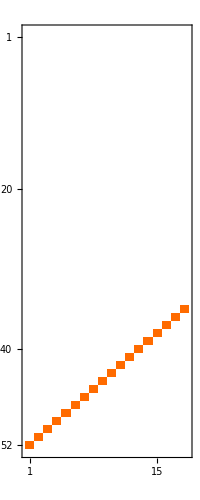

{Null}

```mathematica
Monitor[
Block[{pos=1, quatri=Join[Take[quads,2],Take[alfa1s,2]]},
Table[
Block[
{backup=allGraphs5,
reason="declaring buddies "<>ToString[com]<> " positive.",
reason2="declaring buddies "<>ToString[quads]<> " zero.",
notok, crit,mat},

Table[
allGraphs5[k,"comp"]=Equal;
allGraphs5[k,"compwhy"]=reason2;
allGraphs5[k,"atleast"]=0;
allGraphs5[k,"atleastwhy"]=reason2,
{k,quatri}
];
PropagateAtLeast[];
PropagateAtLeast[];
PropagateAtLeast[];
PropagateComp[];
PropagateComp[];
PropagateComp[];

Clear[RepAtLeast];RepAtLeast[base_]:=RepAtLeast[base]=Table[allGraphs5[key,Bases[base,"Colofour"]]->allGraphs5[key,"atleast"],{key,Bases[base,"AtomKeys"]}];
Clear[RepZero];RepZero[base_]:=RepZero[base]=Table[With[{var=allGraphs5[k,Bases[base,"Colofour"]]},var->If[allGraphs5[k,"comp"]===Equal,0,var]],{k,Bases[base,"AtomKeys"]}];
notok=With[
{base="C",colofour="colofour"},
Select[Keys[allGraphs5],(allGraphs5[#,"atleast"]≠ (allGraphs5[#,colofour]/.RepAtLeast[base]))&]
];
Print[com->Length[notok]];
crit=Reduce[Fold[And,Table[allGraphs5[k,"colofour"]==0,{k,Append[quatri,K5Key]}]]&&Fold[And,Table[Fold[Or,Table[v>0,{v,ListofVars[allGraphs5[k,"colofour"]]}]],{k,notok}]]];
mat=Map[BaseCoeff2[ ListofVars[#],"C"]&,ExpressionToList[crit]]//First;
Print[MatrixRank[mat]];
Print[MatrixPlot[Transpose[Sort[Transpose[Sort[mat]]]]]];
allGraphs5=backup;
],{com,Take[buddyCombinations,1]}
]
],
{com}
]
```